#### Preamble

```mathematica
(*ClearAll["Global`*"]*)
ClearAll@@{$Context<>"*"}
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],10*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
$HistoryLength=5;
```

ScheduledTaskObject[…]

```mathematica
SetDirectory[NotebookDirectory[]]
<<"MaTeX`"
fs = 9;

texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
graphsOpts:= {Mesh-> Full,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> ColorData[3]}
SetOptions[ListLinePlot,graphsOpts];
```

/home/jonathan/Dropbox/WorkWithAlejandro/4.- MScThesis

## Data of materials

```mathematica
h = 4.135668*^-15 (*eV s*);c = 3*^17 (*nm s^-1*);hc = h*c;
materialdata = FileNames["~/Dropbox/RefIndexDataBase/*"]
```

{~/Dropbox/RefIndexDataBase/Ag_nm.csv,~/Dropbox/RefIndexDataBase/Au_2.csv,~/Dropbox/RefIndexDataBase/BK7.csv,~/Dropbox/RefIndexDataBase/Corning.csv,~/Dropbox/RefIndexDataBase/H2O.csv,~/Dropbox/RefIndexDataBase/Si.csv}

The visible range is from 400nm to 780nm  (Handbook of Spectroscopy.Edited by Günter Gauglitz and Tuan Vo-Dinh, Copyright c 2003 WILEY-VCH Verlag GmbH& Co.KGaA,Weinheim, ISBN 3-527-29782-0)
that is in eV

#### Ag: P. B. Johnson and R. W. Christy. Optical Constants of the Noble Metals, Phys. Rev. B 6, 4370-4379 (1972)

```mathematica
nAg = Import[materialdata[[1]],"Data"]; (* {λ [nm], n, κ} donde N = n+iκ y ε = N^2   *) 
nAg = Drop[nAg,1];

nAgFunc=Interpolation[nAg/.{λ_,n_, κ_}-> {λ,n+I κ}];
εAgFunc=Interpolation[nAg/.{λ_,n_, κ_}-> {λ,(n+I κ)^2}];

dummy1=Interpolation[nAg/.{λ_,n_, κ_}-> {λ,n^2-κ^2},Method->"Spline"];
dummy2=Interpolation[nAg/.{λ_,n_, κ_}-> {λ,2*n*κ},Method->"Spline"]
εAgFuncSpline[x_]:=dummy1[x]+I*dummy2[x]
```

InterpolatingFunction[…]

#### Au: Johnson, P. B.; Christy, R. W. (1972). “Optical Constants of the Noble Metals”. Physical Review B. 6 (12): 4370–4379

```mathematica
nAueV = Import[materialdata[[2]],"Data"] ;(*1 es Ag, 2 es Au, 3 es en H2O en nm y 4 es en μm*) (* {nm, n, κ} donde N = n+iκ y ε = N^2   *) 
nAueV  = Drop[Drop[nAueV,-4],2];

nAuFunc=Interpolation[nAueV/.{λ_,n_, κ_}-> { hc /λ,n+I κ}];
εAuFunc=Interpolation[nAueV/.{λ_,n_, κ_}-> {hc/λ,(n+I κ)^2}];

dummy3=Interpolation[nAueV/.{λ_,n_, κ_}-> {hc/λ,n^2-κ^2},Method->"Spline"];
dummy4=Interpolation[nAueV/.{λ_,n_, κ_}-> {hc/λ,2*n*κ},Method->"Spline"]
εAuFuncSpline[x_]:=dummy3[x]+I*dummy4[x]
nAuSize[λ_,a_]:=Sqrt[εAuFuncSpline[λ]-(1-λ/λp^2*1/(1/λ + I/γ))+(1-λ/λp^2*1/(1/λ + I(1/γ+1/γsize)))/.{λp->142.609,γ->14966.2,γsize->(a *2 π c)/(1.4*^15)}(*Values for Au*)]
```

InterpolatingFunction[…]

#### Corning

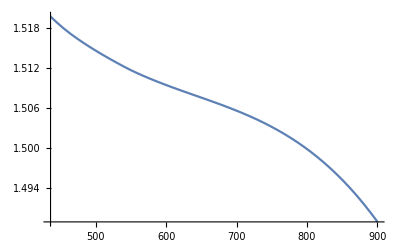

```mathematica
nCor = Import[materialdata[[4]],"Data"] ;(*4 Corning m*) (* {nm, n, κ} donde N = n+iκ y ε = N^2   *) 
nCor  = Drop[nCor,1];

nCorFunc=Interpolation[nCor/.{λ_,n_}-> { λ*1000,n}];
Plot[nCorFunc[λ],{λ,436,900}]
```

#### H2O G. M. Hale and M. R. Querry. Optical constants of water in the 200-nm to 200-µm wavelength region, Appl. Opt. 12, 555-563 (1973)

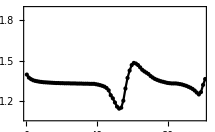
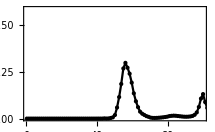

InterpolatingFunction[…]

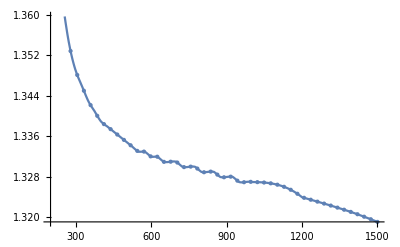

```mathematica
nH2O= Import[materialdata[[5]],"Data"] ;(*4 Corning m*) (* {nm, n, κ} donde N = n+iκ y ε = N^2   *) 
nH2O = Drop[nH2O,1];
ListLinePlot[nH2O[[;;,#]],Mesh->All,DataRange->nH2O[[{1,-1},1]],PlotRange->{{.4,100},{Automatic,Automatic}}]&/@{2,3}

nH2OFunc = Interpolation[nH2O/.{λ_,n_,κ_}-> {λ*1000,n}]
Plot[nH2OFunc[λ],{λ,200,1500},Mesh->Full]
```

#### BK7 G. M. Hale and M. R. Querry. Optical constants of water in the 200-nm to 200-µm wavelength region, Appl. Opt. 12, 555-563 (1973)

InterpolatingFunction[…]

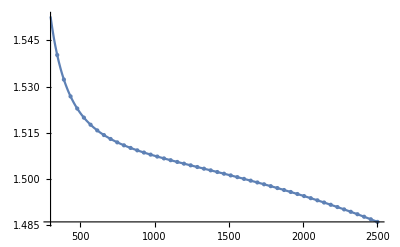

```mathematica
nBK7= Import[materialdata[[3]],"Data"] ;(*4 Corning m*) (* {nm, n, κ} donde N = n+iκ y ε = N^2   *) 
nBK7 = Drop[nBK7,1];

nBK7Func = Interpolation[nBK7[[;;,{1,2}]]]
Plot[nBK7Func[λ],{λ,300,2500},Mesh->Full]
```

#### BK7 vs Cornig

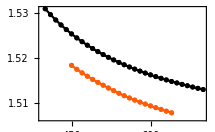

n_Glasses.svg

```mathematica
Table[{x,nBK7Func[x]},{x,400,700,10}];
Table[{x,nCorFunc[x]},{x,450,640,10}];
ListLinePlot[{%%,%}, FrameLabel->{MaTeX["\\lambda\\text{ [nm]}"],Style["Ref. index",texStyle]},
PlotLegends->Placed[(Style[#,texStyle]&/@{"BK7","Corning"}),{Right,Top}]]
Export["n_Glasses.svg",%]
```

## Functions and Models

```mathematica
toMap::usage  = "Converts a non-list entry to a list so Map can be used.";
toMap = If[Length[#]==0,{#},#]&
```

If[Length[#1]==0,{#1},#1]&

## Maxima and Minima

#### movAverage - date - CentralFiniteDifferences

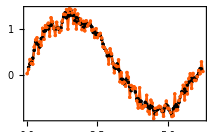
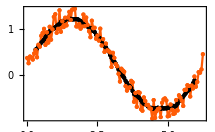
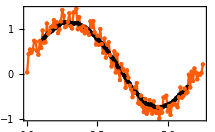

```mathematica
movAverage::usage = "movAverage[list, n] gives the moving average of a one dimensional list with step n";
movAverage[list_,step_]:= Plus @@ Partition[list,Length[list]-step,1]/(step+1)  

sin=Sin[x = Range[0.,2*Pi,.05]];
Table[data = {Transpose[{x[[(i+2)/2;;-(i+2)/2]],movAverage[#,i]}],
	Transpose[{x,#}]} &@ ( sin+RandomReal[.5,Length[x]]);
ListLinePlot[data,DataRange->{0,2Pi}, PlotLegends->Placed[{"Average","Data"},{Right,Top}]],
{i,2,Length[x]/4,10}]
ClearAll[x,sin,data]
```

```mathematica
date::usage="date[] returns a String with the date in format yyyy/mm/dd === hh:mm:ss.";
date[]:=StringJoin@{" === " ,Riffle[#, " === "]," ===\n"}&@ MapThread[StringJoin@Riffle[#1,#2] &,{ Partition[ToString/@ Date[],3] , {"/",":"}}]

date[]
```

=== 2021/11/5 === 12:24:45.269702 ===

CentralFiniteDifferences::DerOrd: The method for error order 3 has not been implemented yet.

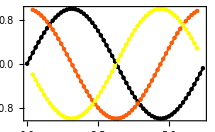

```mathematica
CentralFiniteDifferences::usage="CentralFiniteDifferences[{{x1,y1},{x2,y2},...{xn,yn}}, i] calculates the ith numerical derivative with an O(h^4) error.";
CentralFiniteDifferences::DerOrd="The method for error order `1` has not been implemented yet.";

CentralFiniteDifferences[list_List,order_Integer]/;(If[order<=2,True,Message[CentralFiniteDifferences::DerOrd,order];False]):=Module[{x,y,step,coeff},If[order==0,Return[list]];
{x,y}=Transpose[list];
x=x[[3;;Length[x]-1]];
step=Differences[x]^order;
coeff=Which[order==1,1./{12,-3/2,3/2,-12},order==2,1./{-12,3/4,-2/5,3/4,-12}];
y=If[Mod[order,2]==1,coeff*Drop[#,{3}]&/@Partition[y,5,1],coeff*#&/@Partition[y,5,1]];
Transpose[{Drop[x,-1],Apply[Plus,y,2]/step}]]

(*Examples*)
sin=Sin[x=Range[0.,2*Pi,.1]];
CentralFiniteDifferences[Transpose[{x,sin}],3];

CentralFiniteDifferences[Transpose[{x,sin}],#]&/@{0,1,2}//ListLinePlot[#,PlotLegends->{0,1,2}]&
ClearAll[x,sin]
```

#### GoldenRatioAlgorithm - GoldenRatioMaxima - GoldenRatioMinima

```mathematica
Options[GoldenRatioAlgorithm] = {Method -> "Maxima"};
GoldenRatioAlgorithm[func_, interval_, tol_, OptionsPattern[]]:=Module[{gr =  .5*(Sqrt[5.]+1.) , a,b,c,d,test,extrema },
	test = Which[ OptionValue[Method] == "Maxima", Greater, OptionValue[Method] == "Minima", Less] ;
	{a,b}= Sort[interval];
	c = b - (b-a)/gr;
	d = a + (b-a)/gr;
	While[Abs[c-d] >tol,
		 If[test[func[c],func[d]], b = d, a= c];
		c = b - (b-a)/gr;
		d = a + (b-a)/gr];
	{#,func[#]}&[0.5 *(a+b)]]
```

```mathematica
GoldenRatioMaxima::usage= "GoldenRatioMaxima[func, intervar] calculates the maxima within the interval of the one variable function func empoloying the Golden Ratio Sectioning algorithm. It threads over a list of intervals and returns {x, f(x)}.";
GoldenRatioMaxima::interval = "The interval should be a pair of numbers or a list of pairs.";
Options[GoldenRatioMaxima]={Tolerance ->  1.*^-3};

GoldenRatioMaxima[func_, interval_List, OptionsPattern[]]:=
	If[Length[Dimensions[interval]]==1,
			 If[Length[interval]==2,GoldenRatioAlgorithm[func, interval, OptionValue[Tolerance] ,Method -> "Maxima"] ,Message[GoldenRatioMaxima::interval]],
			If[(Length /@ interval) == ConstantArray[2,Length[interval]], Map[GoldenRatioAlgorithm[func, #, OptionValue[Tolerance] ,Method -> "Maxima"] &, interval], Message[GoldenRatioMaxima::interval]]]

#+{-1,1}*Pi/4. &/@ {0, 2*Pi}
GoldenRatioMaxima[Cos,%]
FindMaximum[Cos[x],{x,2Pi+.003}]
```

{{-0.785398,0.785398},{5.49779,7.06858}}

{{0.000931672,1.},{6.28412,1.}}

{1.,{x→6.28319}}

```mathematica
GoldenRatioMinima::usage= "GoldenRatioMaxima[func, intervar] calculates the minima within the interval of the one variable function func empoloying the Golden Ratio Sectioning algorithm. It threads over a list of intervals and returns {x, f(x)}";
GoldenRatioMinima::interval = "The interval should be a pair of numbers or a list of pairs.";
Options[GoldenRatioMinima]={Tolerance ->  1.*^-3};

GoldenRatioMinima[func_, interval_List, OptionsPattern[]]:=
	If[Length[Dimensions[interval]]==1,
			 If[Length[interval]==2,GoldenRatioAlgorithm[func, interval, OptionValue[Tolerance] ,Method -> "Minima"] ,Message[GoldenRatioMinima::interval]],
			If[(Length /@ interval) == ConstantArray[2,Length[interval]], Map[GoldenRatioAlgorithm[func, #, OptionValue[Tolerance] ,Method -> "Minima"] &, interval], Message[GoldenRatioMinima::interval]]]

#+{-1,1}*Pi/4. &/@ {Pi, 3*Pi}
GoldenRatioMinima[Cos,%, Tolerance -> 1.*^-10]
FindMinimum[Cos[x],{x,Pi+.003}]
```

{{2.35619,3.92699},{8.63938,10.2102}}

{{3.14159,-1.},{9.42478,-1.}}

{-1.,{x→3.14159}}

#### FindExtrema - FindExtremaInterval

```mathematica
FindExtremaInterval::usage = "Find the interval where the maxima or minima of a f : R -> R^n for each component";
FindExtremaInterval[func_, interval_List,h_]:= Module[{test, var,f,df,ddf,min, max,int,len}, 
(*interval = {a,b}, h is a number. \\ {maxs, mins}= intExtrema[f,{a,b}, h]*)
var=Range @@ Flatten[{interval,h}];
If[(len = Length[func[var[[1]]] ])== 0, f = {func /@ var}, f = Transpose[func /@  var]] ;

df= CentralFiniteDifferences[Transpose[{var,#}],1] & /@  f;
ddf =  CentralFiniteDifferences[Transpose[{var,#}],2] & /@  f;

min = max = ConstantArray[{},Length[f]];
Table[ int = Partition[#, 2,1]&@ df[[i,;;,1]];
	test = Partition[#, 2,1]&@ df[[i,;;,2]];
	test = Apply[Times, test, 1];
	If[ddf[[i,#,2]] <0., AppendTo[max[[i]], Flatten[int[[#]]]],
						AppendTo[min[[i]], Flatten[int[[#]]]] ] &/@   Flatten[Position[test, n_/; n<0.]],
{i,Length[f]}];
If[len ==0,{min[[1]], max[[1]]},{min,max}]]
```

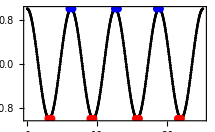

```mathematica
fProof[x_]:=Cos[x]
{min,max} = FindExtremaInterval[fProof,{0.,8Pi},.5] ;

min = {#,-1}&/@Flatten[min];
max = {#, 1}&/@Flatten[max];

ListLinePlot[Table[{x,fProof[x]},{x,0, 8*Pi,.05}], Epilog->{PointSize[.025],Red,Point[min],Blue, Point[max]}]
```

```mathematica
FindExtrema::usage = "Find the specific extrema values of a function f : R -> R^n for each component";
FindExtrema::extType = "Must specify a valid type of extrema point.";

Options[FindExtrema] = {Tolerance -> 1*^-3};
FindExtrema[func_, interval_List,h_, case_String, OptionsPattern[]]:= Module[{grFunc,min, max,len}, 
len = Length[func[interval[[1]]]];
{min, max} =  FindExtremaInterval[func, interval,h];
 Which[case == "Minima",grFunc = GoldenRatioMinima[#1,#2,Tolerance-> OptionValue[Tolerance]]&;
					 If[len ==0, Map[ grFunc[func,# ]&,min],
								Table[Map[ grFunc[func[#][[i]]&,#]& , min[[i]]],{i,len}]],
	case == "Maxima", grFunc = GoldenRatioMaxima[#1,#2,Tolerance-> OptionValue[Tolerance]]&;
					If[len ==0, Map[ grFunc[func,# ]&,max],
								Table[Map[ grFunc[func[#][[i]]&,#]& , max[[i]]],{i,len}]],
	case == "Both", {grFunc = GoldenRatioMinima[#1,#2,Tolerance-> OptionValue[Tolerance]]&;
					If[len ==0, Map[ grFunc[func,# ]&,min],
								Table[Map[ grFunc[func[#][[i]]&,#]& , min[[i]]],{i,len}]],
					grFunc = GoldenRatioMaxima[#1,#2,Tolerance-> OptionValue[Tolerance]]&;
					If[len ==0, Map[ grFunc[func,# ]&,max],
								Table[Map[ grFunc[func[#][[i]]&,#]& , max[[i]]],{i,len}]]
					},
		True, Message[FindExtrema::extType]]]
```

True

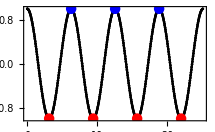

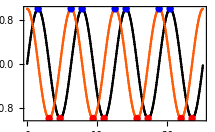

```mathematica
fProof[x_]:=Cos[x]
{min, max, both} =FindExtrema[fProof,{0.,8Pi},.5,#] &/@{"Minima","Maxima", "Both"};
{min,max} == both 
ListLinePlot[Table[{x,fProof[x]},{x,0, 8*Pi,.05}], Epilog->{PointSize[.035],Red,Point[min],Blue, Point[max]}]

fProof[x_]:={Sin[x],Cos[x]}
{min,max}  = Flatten[#,1]&/@FindExtrema[fProof,{0.,8Pi},.5, "Both"];
ListLinePlot[Transpose@Table[{{x,#1},{x,#2}}&@@fProof[x],{x,0, 8*Pi,.05}],  Epilog->{PointSize[.025],Red,Point[min],Blue, Point[max]}]
```

## Optics (Fresnel, Landau, TransferMatrix, Mie, CSM, DM)

### FresnelReflectionS - FresnelReflectionP - FresnelTransmissionS - FresnelImpedanceS - FresnelImpedance

```mathematica
FresnelCoefficient::angDomain = "The incident angle `1` must be between 0 and Pi/2.";
FresnelCoefficient::refIndeces = "The length of `1` must equal the length of `2`.";

FresnelReflectionS::usage  = "It returns the Fresnel amplitude coefficient of reflection for S polarization. The results is an array of dimensions Length[ang] x Length[ni]";
FresnelReflectionP::usage  = "It returns the Fresnel amplitude coefficient of reflection for P polarization. The results is an array of dimensions Length[ang] x Length[ni]";FresnelTransmissionS::usage  = "It returns the Fresnel amplitude coefficient of transmission for S polarization. The results is an array of dimensions Length[ang] x Length[ni]";
FresnelTransmissionP::usage  = "It returns the Fresnel amplitude coefficient of transmission for P polarization. The results is an array of dimensions Length[ang] x Length[ni]";
```

#### FresnelReflectionS

```mathematica
FresnelReflectionS[ang_,{ni_,nt_}]:= Module[{ m = toMap[nt/ni],thetai = toMap[ang], costhi, costht, rs},
	If[ang<0 || Pi/2.< ang, Return[Message[FresnelCoefficient::angDomain, ang]]];
	If[Length[ni]!= Length[nt], Return[Message[FresnelCoefficient::refIndeces, ni, nt]]];
		costhi = Cos[thetai];
		costht = Outer[Sqrt[#2^2-Sin[#1]^2]& ,  thetai,m];
		rs = Divide[Plus[#1,-#2],Plus[#1,+ #2]] & @@ {costhi,costht};
		Which[Length[ni]==Length[ang]==0, rs[[1,1]],
			Length[ni]==0 || Length[ang]== 0, Flatten[rs],
			True, rs]
]
```

#### FresnelReflectionP

```mathematica
FresnelReflectionP[ang_,{ni_,nt_}]:= Module[{ m = toMap[nt/ni],thetai = toMap[ang], Ncosthi, costht, rp},
	If[ang<0 || Pi/2.< ang, Return[Message[FresnelCoefficient::angDomain, ang]]];
	If[Length[ni]!= Length[nt], Return[Message[FresnelCoefficient::refIndeces, ni, nt]]];
		Ncosthi = Outer[#2^2 * Cos[#1]& ,  thetai,m];
		costht = Outer[Sqrt[#2^2-Sin[#1]^2]& ,  thetai,m];
		rp = Divide[Plus[#1,-#2],Plus[#1,+ #2]] & @@ {Ncosthi,costht};
		Which[Length[ni]==Length[ang]==0, rp[[1,1]],
			Length[ni]==0 || Length[ang]== 0, Flatten[rp],
			True, rp]
]
```

#### FresnelTransmissionS

```mathematica
FresnelTransmissionS[ang_,{ni_,nt_}]:= Module[{ m = toMap[nt/ni],thetai = toMap[ang], costhi, costht, ts},
	If[ang<0 || Pi/2.< ang, Return[Message[FresnelCoefficient::angDomain, ang]]];
	If[Length[ni]!= Length[nt], Return[Message[FresnelCoefficient::refIndeces, ni, nt]]];
		costhi = Cos[thetai]; (*[[ang]]*)
		costht = Sqrt[m^2 -#^2]&/@Sin[thetai]; (*[[ang, ni]] *)
		ts = Divide[2*#1,Plus[#1, #2]] & @@ {costhi,costht};
		Which[Length[ni]==Length[ang]==0, ts[[1,1]],
			Length[ni]==0 || Length[ang]== 0, Flatten[ts],
			True, ts]
]
```

#### FresnelTransmissionP

```mathematica
FresnelTransmissionP[ang_,{ni_,nt_}]:= Module[{ m = toMap[nt/ni],thetai = toMap[ang], Ncosthi, costht, tp},
	If[ang<0 || Pi/2.< ang, Return[Message[FresnelCoefficient::angDomain, ang]]];
	If[Length[ni]!= Length[nt], Return[Message[FresnelCoefficient::refIndeces, ni, nt]]];
		Ncosthi = Outer[#2^2 * Cos[#1]& ,  thetai,m];
		costht = Outer[Sqrt[#2^2-Sin[#1]^2]& ,  thetai,m];
		tp = Divide[ 2*#1  ,Plus[#1,#2]] & @@ {Ncosthi,costht};
		tp = Map[#/m & ,tp];
		Which[Length[ni]==Length[ang]==0, tp[[1,1]],
			Length[ni]==0 || Length[ang]== 0, Flatten[tp],
			True, tp]
]
```

#### FresnelImpedance

```mathematica
FresnelImpedance[ang_,{ni_,nt_}]:= Module[{ thetai = toMap[ang], m = toMap[nt/ni], imp},
	If[ang<0 || Pi/2.< ang, Return[Message[FresnelCoefficient::angDomain, ang]]];
	If[Length[ni]!= Length[nt], Return[Message[FresnelCoefficient::refIndeces, ni, nt]]];
		imp = Re@Outer[(Sqrt[#2^2-Sin[#1]^2]/Cos[#1])& ,  thetai,m];
		
		Which[Length[ni]==Length[ang]==0, imp[[1,1]],
			Length[ni]==0 || Length[ang]== 0, Flatten[imp],
			True, imp]
]
```

#### FIgures

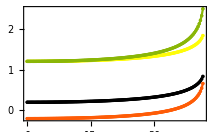

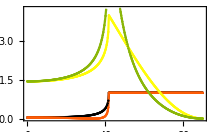

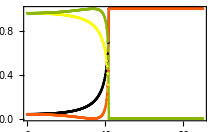

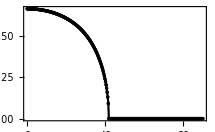

```mathematica
angle = Range[0,Pi/2,.005];
ind = {1.5,1};
fresnel = Table[func[angle,ind],{func,{FresnelReflectionS,FresnelReflectionP,FresnelTransmissionS,FresnelTransmissionP}}];
ListLinePlot[fresnel, DataRange->{0,90}, PlotLegends->Automatic]
ListLinePlot[Chop[#*Conjugate[#]]&@fresnel, DataRange->{0,90}]
ListLinePlot[(FresnelImpedance[angle,#]&/@{{1,1},{1,1},ind, ind} )*  ( Chop[#*Conjugate[#]]&@fresnel),DataRange->{0,90}]
ListLinePlot[FresnelImpedance[angle, ind],DataRange->{0,90}]

ClearAll[angle,fresnel]
```

### Landau3MediaReflectionS - Landau3MediaReflectionP - Landau3MediaElipsometry

```mathematica
Landau3Media::thick = "The thickness `1` must be a scalar.";
Landau3Media::lda = "The Length of `1`, `2`, `3` and `4` must be the same.";

Landau3MediaReflectionS::usage = "It returns the reflection amplitud coeficient of a three media system, where an anisotropy refractive index can be considered.";
Landau3MediaReflectionP::usage = "It returns the reflection amplitud coeficient of a three media system, where an anisotropy refractive index can be considered.";
Landau3MediaElipsometry::usage = "It returns the elipsometric parameters {Psi,Delta} in radians given by rp/rs = Tan[Psi]*Exp[I*Delta]. An anisotropic refractive index can be taken into account.";
```

#### Landau3MediaReflectionS

```mathematica
Landau3MediaReflectionS[ang_,{n1_,n2_,n3_},lda_,thick_]:= Module[{thetai = toMap[ang], epsilon = {n1,n2,n3}^2 ,kz, dkz, r12,r23,r123,psi} ,
If[Length[thick]!= 0, Return[Message[Landau3Media::thick, thick]]];
If[ Length[lda]== 0,
If[!Apply[Equal, Length /@ Prepend[epsilon[[{1,3}]],lda] ]&& Length[epsilon[[2,1]]] == Length[lda],
		Return[Message[Landau3Media::lda, n1,n2,n3,lda]],
	epsilon = Map[toMap,epsilon ,2];epsilon[[2]] ={Flatten[epsilon[[2]]]}],
If[!Apply[Equal, Length /@ Prepend[epsilon,lda]],Return[Message[Landau3Media::lda, n1,n2,n3,lda]]]
];

If[Length[Dimensions[epsilon[[2]]]] == 2,  (*If anisotropic Film*)
		epsilon[[2]] = epsilon[[2,;;,1]]]; (*We only consider the parallel component*)

kz = Map[# * Sin[thetai]^2&, epsilon[[1]]]; (* (n1*Sin[angle])^2 , [[n1, angle]]*)
kz = Sqrt[# -  kz ]&/@   epsilon  (*[[3(medium), ni, angle]]*);

dkz = Partition[kz, 2, 1]; 
 r12 = Apply[Divide  , {Plus[#1,-#2],Plus[#1,#2]}]& @@ dkz[[1]];
 r23 =Apply[ Divide  , {Plus[#1,-#2],Plus[#1,#2]}]&@@ dkz[[2]];

psi = thick* 2*Pi * (kz[[2]] / toMap[lda]);
r123 = r12+r23*Exp[2*I*psi];
r123/= 1+r12*r23*Exp[2*I*psi];

Which[Length[n1]==Length[ang]==0, r123[[1,1]],
	Length[n1]==0 || Length[ang]== 0, Flatten[r123],
	True, Transpose[r123]]
]
```

0.0202748

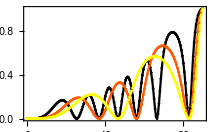

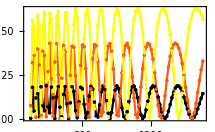

```mathematica
Chop[#*Conjugate[#]] &@Landau3MediaReflectionS[66*Pi/180.,{1,1.5,1},500.,500*8]

ang = Range[0,90,.5]*Pi/180.;
lda = {500,1000,1500};
n3 = n1 = 1 &/@lda;
n2 =  {1.5,1.5}  &/@ lda;

Chop[#*Conjugate[#]]&@Landau3MediaReflectionS[ang,{n1,n2,n3},lda,500*8];
Transpose@%//ListLinePlot[#,DataRange->{0,90}]&

ang = {25,55,66}*Pi/180.;
lda = Range[500,1500,10.];
n3 = n1 = 1 &/@lda;
n2 =  {1.5,1.5}  &/@ lda;

Chop[#*Conjugate[#]]&@Landau3MediaReflectionS[ang,{n1,n2,n3},lda,500*8];
%//ListLinePlot[#,DataRange->{500,1500}]&
```

#### Landau3MediaReflectionP

```mathematica
Landau3MediaReflectionP[ang_,{n1_,n2_,n3_},lda_,thick_]:= Module[{thetai = toMap[ang], epsilon = {n1,n2,n3}^2 ,kz,  r12,r23,r123,psi, ani} ,
If[Length[thick]!= 0, Return[Message[Landau3Media::thick, thick]]];
If[ Length[lda]== 0,
If[!Apply[Equal, Length /@ Prepend[epsilon[[{1,3}]],lda] ]&& Length[epsilon[[2,1]]] == Length[lda],
		Return[Message[Landau3Media::lda, n1,n2,n3,lda]],
	epsilon = Map[toMap,epsilon ,2];epsilon[[2]] ={Flatten[epsilon[[2]]]}],
If[!Apply[Equal, Length /@ Prepend[epsilon,lda]],Return[Message[Landau3Media::lda, n1,n2,n3,lda]]]
];

ani = ConstantArray[1.,{3,Length[epsilon[[1]]]}];
(*Return[epsilon[[2]]];*)

If[Length[Dimensions[epsilon[[2]]]] == 2,  (*If anisotropic Film*)
		ani = Map[ If[Length[#]==2, Divide@@ # ,1.]& , epsilon,{2}];
		epsilon[[2]] = epsilon[[2,;;,1]]]; (*We only consider the parallel component*)

kz = Map[# * Sin[thetai]^2&,epsilon[[1]]]; (* (eps1*Sin[angle])^2 , [[n1, angle]]*)
kz = kz*# &/@ ani; (*ani*Sin[angle]*eps1  [[3,n1,angle]]*)
kz = Sqrt[epsilon-  kz]  (*[[3(medium), ni, angle]]*);

 r12 = Apply[Divide  , {Plus[#1,-#2],Plus[#1,#2]}]& @@ (epsilon[[{2,1}]]*kz[[{1,2}]]);
 r23 =Apply[ Divide  , {Plus[#1,-#2],Plus[#1,#2]}]&@@ (epsilon[[{3,2}]]*kz[[{2,3}]]);

psi = thick* 2*Pi * (kz[[2]] / toMap[lda]);
r123 = r12+r23*Exp[2*I*psi];
r123/= 1+r12*r23*Exp[2*I*psi];

Which[Length[n1]==Length[ang]==0, r123[[1,1]],
	Length[n1]==0 || Length[ang]== 0, Flatten[r123],
	True, Transpose[r123]]
]
```

0.000873024

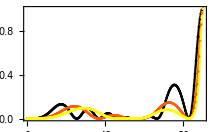

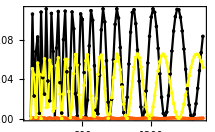

```mathematica
Chop[#*Conjugate[#]] &@Landau3MediaReflectionP[66*Pi/180.,{1,1.5,1},500.,500*8]

ang = Range[0,90,.5]*Pi/180.;
lda = {500,1000,1500};
n3 = n1 = 1 &/@lda;
n2 = {1.5,1.5}  &/@ lda;

Chop[#*Conjugate[#]]&@Landau3MediaReflectionP[ang,{n1,n2,n3},lda,500*8];
Transpose@%//ListLinePlot[#,DataRange->{0,90}, PlotRange->All]&

ang = {25,55,66}*Pi/180.;
lda = Range[500,1500,10.];
n3 = n1 = 1 &/@lda;
n2 =  {1.5,1.5}  &/@ lda;

Chop[#*Conjugate[#]]&@Landau3MediaReflectionP[ang,{n1,n2,n3},lda,500*8];
%//ListLinePlot[#,DataRange->{500,1500}]&
```

#### Landau3MediaElipsometry

```mathematica
Landau3MediaElipsometry[ang_,{n1_,n2_,n3_},lda_,thick_]:= {ArcTan[Abs[#]],Arg[#]}&@ (Divide@@ Through[{Landau3MediaReflectionP,Landau3MediaReflectionS}[ang,{n1,n2,n3},lda,thick]] (*[[pol (2), ang, lda]]*))
```

{0.204604,-0.0656263}

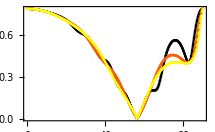
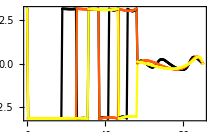

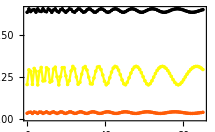
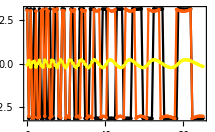

```mathematica
Landau3MediaElipsometry[66*Pi/180.,{1,1.5,1},500.,500*8]

ang = Range[0,90,.5]*Pi/180.;
lda = {500,1000,1500};
n3 = n1 = 1 &/@lda;
n2 = {1.5,1.5}  &/@ lda;

Landau3MediaElipsometry[ang,{n1,n2,n3},lda,500*8];
ListLinePlot[Transpose[#],DataRange->{0,90}, PlotRange->All]& /@ %

ang = {25,55,66}*Pi/180.;
lda = Range[500,1500,10.];
n3 = n1 = 1 &/@lda;
n2 =  {1.5,1.5}  &/@ lda;

Landau3MediaElipsometry[ang,{n1,n2,n3},lda,500*8];
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ %
```

### TransferMatrixS - TransferMatrixP - TransferMatrixElipsometry - TransferMatrixImpedanceS - TransferMatrixImpedanceP

```mathematica
TransferMatrix::thick = "This distances `1` must be a scalar quantity or a list of scalar qunatities.";
TransferMatrix::ind = "This length of `1` must be a the length of `2`  minus 2.";
TransferMatrix::len = "This length of `1` must equal the length of each element of `2`";
TransferMatrix::ani = "This length of `1` must equal the length of each element of `2`";

TransferMatrixS::usage ="It returns the reflection and transmission {r,t} amplitude coefficients for a stratified media; it can consider anisotropic refractive indices.";
TransferMatrixP::usage ="It returns the reflection and transmission {r,t} amplitude coefficients for a stratified media; it can consider anisotropic refractive indices.";
TransferMatrixElipsometry::usage ="IIt returns the elipsometric parameters {Psi,Delta} in radians given by rp/rs = Tan[Psi]*Exp[I*Delta] for a stratified media; it can consider anisotropic refractive indices.";
```

#### TransferMatrixS

```mathematica
TransferMatrixS[ang_,indices_, lda_, distances_]:=Module[{thetai = toMap[ang], indicesPar, dist,  phase,p,Z0,mMatrix,rt={0,0} ,m},
Z0 = 120.Pi;(*Sqrt[mu0/eps0]=Impredance free Space*)
dist = Flatten[{0.,distances,0.},1]; (*[[dist]]*)
indicesPar = toMap /@ indices ;  (*[[dist, lda]]*)

If[ !Apply[Equal, Length/@  dist], Return[Message[TransferMatrix::thick,distances]]];
If[Length[indices]!= Length[dist], Return[Message[TransferMatrix::ind,distances,indices]]];
If[Length /@ Select[indices, Length[#]== lda&]  != Length[dist], Return[0]];
If[Length[lda]==0, (*We take only the parallel contribution of the refractive indices*)
If[Flatten [Dimensions /@ indices] != {} ,
(*If not isotropic*)indicesPar = toMap /@  (toMap /@ indices)[[;;,1]];
					If[!Apply[Equal,  Dimensions /@  Append[Select[indices, Length[#]!= 0 &] ,{0,0}] ] , Return[Message[TransferMatrix::len,lda,indices]]]],
If[Flatten[Length/@Dimensions/@ Prepend[indices,#]]!=ConstantArray[1,Length[#]]&[lda],
(*If not isotropic *) indicesPar = Map[If[Length[Dimensions[#]]==2,#[[;;,1]],#]&, indices]]
];
If[!Apply[Equal, Length/@ Prepend[indicesPar,toMap[lda]]], Return[Message[TransferMatrix::len,lda,indices]]];

p = (#*Sin[thetai])^2 &/@indicesPar[[1]]; (*(n1Sin[th_i])^2   [[lda, ang]]*)
p =  (1/Z0)*(Sqrt[#^2 - p]&/@ indicesPar) ; (*[[dist, lda, ang]] *)
phase =((2.*Pi/toMap[lda])*#&/@  p* Z0 )* dist ; (* kz*d   [[dist, lda, ang]]*)

m = {{Cos[#1], - I* Sin[#1]/#2},{-I*#2*Sin[#1], Cos[#1]}}&[phase, p];  (*[[ren, col, dist, lda, ang]]*)
m  = Transpose[m,{4,5,3,1,2}];  (*[[lda, ang, dist, ren, col]]*)
m = Array[Apply[Dot,m[[#1,#2]]]&,Length/@{toMap[lda], thetai} ]; (*[[lda, ang, ren, col]]*)
m = Transpose[m, {3,4,1,2}]; (*[[ren, col, lda, ang]]*)

rt[[1]] =  (m[[1,1]]+m[[1,2]]*p[[-1]])*p[[1]]-(m[[2,1]]+m[[2,2]]*p[[-1]]);
rt[[1]] /=( (m[[1,1]]+m[[1,2]]*p[[-1]])*p[[1]]+(m[[2,1]]+m[[2,2]]*p[[-1]]));
rt[[2]] = 2 *p[[1]]/( (m[[1,1]]+m[[1,2]]*p[[-1]])*p[[1]]+(m[[2,1]]+m[[2,2]]*p[[-1]]));
(*rt [[rt(2), lda, ang]]*)
rt = Transpose[rt,{1,3,2}]; (*rt [[rt(2), ang, lda]]*)

Which[Length[lda]==Length[ang]==0, rt[[;;, 1,1]],
	Length[lda]==0 , rt[[;;,;;,1]],
	Length[ang]==0, rt[[;;,1,;;]],
	True, rt]
]
```

0.0202748

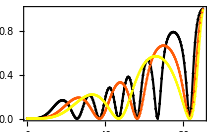

-Graphics-

```mathematica
TransferMatrixS[66*Pi/180.,{1,1.5,1},500.,500*8] [[1]];
Chop[#*Conjugate[#]]&@ %

ang = Range[0,90-.5,.5]*Pi/180.;
lda = {500,1000,1500};
n3 = n1 = 1 &/@lda;
n2 = 1.5  &/@ lda;
TransferMatrixS[ang,{n1,n2,n3}, lda, 500*8] [[1]];
Chop[#*Conjugate[#]]&@%;
Transpose@%//ListLinePlot[#,DataRange->{0,90}]&


ang = {25,55,66}*Pi/180.;
lda = Range[500,1500,10.];
n3 = n1 = 1 &/@lda;
n2 = 1.5  &/@ lda;
Chop[#*Conjugate[#]]&@TransferMatrixS[ang,{n1,n2,n3},lda,500*8][[1]];
%//ListLinePlot[#,DataRange->{500,1500}]&
```

#### TransferMatrixImpedanceS

```mathematica
TransferMatrixImpedanceS[ang_,indices_, lda_, distances_]:=Module[{thetai = toMap[ang], indicesPar, dist,  p},
dist = Flatten[{0.,distances,0.},1]; (*[[dist]]*)
indicesPar = toMap /@ indices ;  (*[[dist, lda]]*)

If[ !Apply[Equal, Length/@  dist], Return[Message[TransferMatrix::thick,distances]]];
If[Length[indices]!= Length[dist], Return[Message[TransferMatrix::ind,distances,indices]]];
If[Length /@ Select[indices, Length[#]== lda&]  != Length[dist], Return[0]];
If[Length[lda]==0, (*We take only the parallel contribution of the refractive indices*)
If[Flatten [Dimensions /@ indices] != {} ,
(*If not isotropic*)indicesPar = toMap /@  (toMap /@ indices)[[;;,1]];
					If[!Apply[Equal,  Dimensions /@  Append[Select[indices, Length[#]!= 0 &] ,{0,0}] ] , Return[Message[TransferMatrix::len,lda,indices]]]],
If[Flatten[Length/@Dimensions/@ Prepend[indices,#]]!=ConstantArray[1,Length[#]]&[lda],
(*If not isotropic *) indicesPar = Map[If[Length[Dimensions[#]]==2,#[[;;,1]],#]&, indices]]
];
If[!Apply[Equal, Length/@ Prepend[indicesPar,toMap[lda]]], Return[Message[TransferMatrix::len,lda,indices]]];

p = (#*Sin[thetai])^2 &/@indicesPar[[1]]; (*(n1Sin[th_i])^2   [[lda, ang]]*)
p =  (Sqrt[#^2 - p]&/@ indicesPar) ; (*[[dist, lda, ang]] *)

p = Re [Divide @@ p[[{-1,1}]] ];

Which[Length[lda]==Length[ang]==0, p[[1,1]],
	Length[lda]==0 , p[[1]],
	Length[ang]==0, p[[;;,1]],
	True, Transpose[p]]
]
```

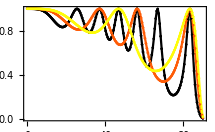

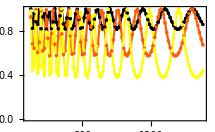

```mathematica
ang = Range[0,90-.5,.5]*Pi/180.;
lda = {500,1000,1500};
n3 = n1 = 1 &/@lda;
n2 = 1.5  &/@ lda;

Through[{TransferMatrixImpedanceS, TransferMatrixS}[ang,{n1,n2,n3}, lda, 500*8] ];
#1*Chop[#2[[2]]*Conjugate[#2[[2]]]]&@@%;
Transpose@%//ListLinePlot[#,DataRange->{0,90}]&


ang = {25,55,66}*Pi/180.;
lda = Range[500,1500,10.];
n3 = n1 = 1 &/@lda;
n2 = 1.5  &/@ lda;
Through[{TransferMatrixImpedanceS, TransferMatrixS}[ang,{n1,n2,n3}, lda, 500*8] ];
#1*Chop[#2[[2]]*Conjugate[#2[[2]]]]&@@%;
%//ListLinePlot[#,DataRange->{500,1500}]&
```

#### TransferMatrixP

```mathematica
TransferMatrixP[ang_,indices_, lda_, distances_]:=Module[{thetai = toMap[ang], indicesPar, dist,  phase,q,Z0,mMatrix,rt={0,0} ,m, ani},
Z0 = 120.Pi;(*Sqrt[mu0/eps0]=Impredance free Space*)
dist = Flatten[{0.,distances,0.},1]; (*[[dist]]*)
indicesPar = toMap /@ indices ;  (*[[dist, lda]]*)
ani = ConstantArray[1.,Dimensions[indicesPar]];

If[ !Apply[Equal, Length/@  dist], Return[Message[TransferMatrix::thick,distances]]];
If[Length[indices]!= Length[dist], Return[Message[TransferMatrix::ind,distances,indices]]];
If[Length /@ Select[indices, Length[#]== lda&]  != Length[dist], Return[0]];
If[Length[lda]==0, (*We take only the parallel contribution of the refractive indices*)
If[Flatten [Dimensions /@ indices] != {} ,
(*If not isotropic*) ani = Map[ If[Length[#]==2, Divide@@ # ,1.]& , indices];
					indicesPar = toMap /@  (toMap /@ indices)[[;;,1]];
					If[!Apply[Equal,  Dimensions /@  Append[Select[indices, Length[#]!= 0 &] ,{0,0}] ] , Return[Message[TransferMatrix::len,lda,indices]]]],
If[Flatten[Length/@Dimensions/@ Prepend[indices,#]]!=ConstantArray[1,Length[#]]&[lda],
(*If not isotropic *)  ani =Map[ If[Length[#]==2, Divide@@ # ,1.]& , indices, {2}];
					indicesPar = Map[If[Length[Dimensions[#]]==2,#[[;;,1]],#]&, indices]]
];
If[!Apply[Equal, Length/@ Prepend[indicesPar,toMap[lda]]], Return[Message[TransferMatrix::len,lda,indices]]];

q = #*Sin[thetai] &/@indicesPar[[1]]; (*(n1Sin[th_i])   [[lda, ang]]*)
q = #*q &/@ ani; (*a*n* Sin[thi]   [[dist, lda, ang]]*)
q =  Z0*Sqrt[indicesPar^2 - q^2] ; (*[[dist, lda, ang]] *)
phase =((2.*Pi/toMap[lda])*#&/@  (q/ Z0) )* dist ; (* kz*d   [[dist, lda, ang]]*)
q /= indicesPar^2;

m = {{Cos[#1], - I* Sin[#1]/#2},{-I*#2*Sin[#1], Cos[#1]}}&[phase, q];  (*[[ren, col, dist, lda, ang]]*)
m  = Transpose[m,{4,5,3,1,2}];  (*[[lda, ang, dist, ren, col]]*)
m = Array[Apply[Dot,m[[#1,#2]]]&,Length/@{toMap[lda], thetai} ]; (*[[lda, ang, ren, col]]*)
m = Transpose[m, {3,4,1,2}]; (*[[ren, col, lda, ang]]*)

rt[[1]] =  (m[[1,1]]+m[[1,2]]*q[[-1]])*q[[1]]-(m[[2,1]]+m[[2,2]]*q[[-1]]);
rt[[1]] /=( (m[[1,1]]+m[[1,2]]*q[[-1]])*q[[1]]+(m[[2,1]]+m[[2,2]]*q[[-1]]));
rt[[2]] = 2 *q[[1]]/( (m[[1,1]]+m[[1,2]]*q[[-1]])*q[[1]]+(m[[2,1]]+m[[2,2]]*q[[-1]]));
(*rt [[rt(2), lda, ang]]*)
rt = Transpose[rt,{1,3,2}]; (*rt [[rt(2), ang, lda]]*)

Which[Length[lda]==Length[ang]==0, rt[[;;, 1,1]],
	Length[lda]==0 , rt[[;;,;;,1]],
	Length[ang]==0, rt[[;;,1,;;]],
	True, rt]
]
```

-0.00340336+0.0293503 ⅈ

0.000873024

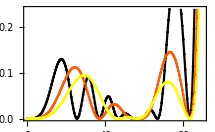

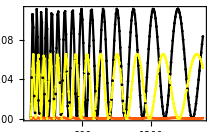

```mathematica
TransferMatrixP[66*Pi/180.,{1,{1.5,1.5},1},500.,500*8] [[1]]
Chop[#*Conjugate[#]]&@ %

ang = Range[0,90-.5,.5]*Pi/180.;
lda = {500,1000,1500};
n3 = n1 = 1 &/@lda;
n2 = 1.5  &/@ lda;
TransferMatrixP[ang,{n1,n2,n3}, lda, 500*8] [[1]];
Chop[#*Conjugate[#]]&@%;
Transpose@%//ListLinePlot[#,DataRange->{0,90}]&


ang = {25,55,66}*Pi/180.;
lda = Range[500,1500,5.];
n3 = n1 = 1 &/@lda;
n2 = {1.5,1.5}  &/@ lda;
Chop[#*Conjugate[#]]&@TransferMatrixP[ang,{n1,n2,n3},lda,500*8][[1]];
%//ListLinePlot[#,DataRange->{500,1500}]&
```

#### TransferMatrixImpedanceP

```mathematica
TransferMatrixImpedanceP[ang_,indices_, lda_, distances_]:=Module[{thetai = toMap[ang], indicesPar, dist,  phase,q, ani},
dist = Flatten[{0.,distances,0.},1]; (*[[dist]]*)
indicesPar = toMap /@ indices ;  (*[[dist, lda]]*)
ani = ConstantArray[1.,Dimensions[indicesPar]];

If[ !Apply[Equal, Length/@  dist], Return[Message[TransferMatrix::thick,distances]]];
If[Length[indices]!= Length[dist], Return[Message[TransferMatrix::ind,distances,indices]]];
If[Length /@ Select[indices, Length[#]== lda&]  != Length[dist], Return[0]];
If[Length[lda]==0, (*We take only the parallel contribution of the refractive indices*)
If[Flatten [Dimensions /@ indices] != {} ,
(*If not isotropic*) ani = Map[ If[Length[#]==2, Divide@@ # ,1.]& , indices];
					indicesPar = toMap /@  (toMap /@ indices)[[;;,1]];
					If[!Apply[Equal,  Dimensions /@  Append[Select[indices, Length[#]!= 0 &] ,{0,0}] ] , Return[Message[TransferMatrix::len,lda,indices]]]],
If[Flatten[Length/@Dimensions/@ Prepend[indices,#]]!=ConstantArray[1,Length[#]]&[lda],
(*If not isotropic *)  ani =Map[ If[Length[#]==2, Divide@@ # ,1.]& , indices, {2}];
					indicesPar = Map[If[Length[Dimensions[#]]==2,#[[;;,1]],#]&, indices]]
];
If[!Apply[Equal, Length/@ Prepend[indicesPar,toMap[lda]]], Return[Message[TransferMatrix::len,lda,indices]]];

q = (#*Sin[thetai])^2 &/@indicesPar[[1]]; (*(n1Sin[th_i])^2   [[lda, ang]]*)
q = #*q &/@ ani; (*a*(n1 Sin[thi])^2   [[dist, lda, ang]]*)
q =  Sqrt[indicesPar^2 - q] /indicesPar^2; (*[[dist, lda, ang]] *)
q = Re[Divide @@ q[[{-1,1}]]];

Which[Length[lda]==Length[ang]==0, q[[ 1,1]],
	Length[lda]==0 , q[[1]],
	Length[ang]==0, q[[;;,1]],
	True, Transpose[q]]
]
```

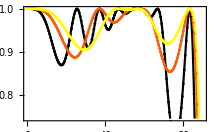

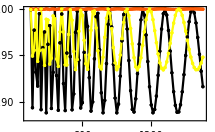

```mathematica
ang = Range[0,90-.5,.5]*Pi/180.;
lda = {500,1000,1500};
n3 = n1 = 1 &/@lda;
n2 = 1.5  &/@ lda;

Through[{TransferMatrixImpedanceP, TransferMatrixP}[ang,{n1,n2,n3}, lda, 500*8] ];
#1*Chop[#2[[2]]*Conjugate[#2[[2]]]]&@@%;
Transpose@%//ListLinePlot[#,DataRange->{0,90}]&


ang = {25,55,66}*Pi/180.;
lda = Range[500,1500,10.];
n3 = n1 = 1 &/@lda;
n2 = 1.5  &/@ lda;
Through[{TransferMatrixImpedanceP, TransferMatrixP}[ang,{n1,n2,n3}, lda, 500*8] ];
#1*Chop[#2[[2]]*Conjugate[#2[[2]]]]&@@%;
%//ListLinePlot[#,DataRange->{500,1500}]&
```

#### TransferMatrixElipsometry

```mathematica
TransferMatrixElipsometry[ang_,indices_,lda_,distances_]:= {ArcTan[Abs[#]],Arg[#]}&@ (Divide@@ (Through[{TransferMatrixP,TransferMatrixS}[ang,indices,lda,distances]])[[;;,1]] (*[[pol (2), ang, lda]]*))
```

{0.204604,-0.0656263}

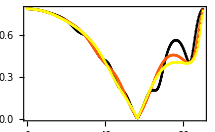
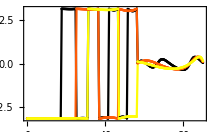

{-Graphics-,-Graphics-}

```mathematica
TransferMatrixElipsometry[66*Pi/180.,{1,1.5,1},500.,500*8]

ang = Range[.5,90-.5,.5]*Pi/180.;
lda = {500,1000,1500};
n3 = n1 = 1 &/@lda;
n2 = {1.5,1.5}  &/@ lda;

TransferMatrixElipsometry[ang,{n1,n2,n3},lda,500*8];
ListLinePlot[Transpose[#],DataRange->{0,90}, PlotRange->All]& /@ %

ang = {25,55,66}*Pi/180.;
lda = Range[500,1500,10.];
n3 = n1 = 1 &/@lda;
n2 =  {1.5,1.5}  &/@ lda;

TransferMatrixElipsometry[ang,{n1,n2,n3},lda,500*8];
ListLinePlot[#,DataRange->{0,90}, PlotRange->All]& /@ %
```

### MieCoefficient - MiePi - MiTau - MieScatteringAmplitude012

```mathematica
MieCoefficient::usage="MieCoefficient[n,x,m] give the Mie Coefficients for a given size parameter x and a relative refractive index ; this functions threads over n.";
MieCoefficient::list="Both `1`and `2` must be scalar quantities.";
MieCoefficient::int = "Parameter `1` must be an integer number.";
```

#### MieCoefficient - MieCoefficientInt

```mathematica
MieCoefficient[n_,x_,m_]:=Module[{an,bn,psiMX,dpsiMX,psiX,dpsiX,xiX,dxiX},
If[!Apply[Equal,Length/@{x,m,0}],Return[Message[MieCoefficient::list,x,m]]];

{psiMX,dpsiMX}={m*x*#,-n*#+m*x*SphericalBesselJ[n-1,m*x]}&@SphericalBesselJ[n,m*x];
{psiX,dpsiX}={x*#,-n*#+x*SphericalBesselJ[n-1,x]}&@SphericalBesselJ[n,x];
{xiX,dxiX}={psiX,dpsiX}+I*{x*#,-n*#+x*SphericalBesselY[n-1,x]}&@SphericalBesselY[n,x];

an=(m*psiMX*dpsiX-psiX*dpsiMX)/(m*psiMX*dxiX-xiX*dpsiMX);
bn=(psiMX*dpsiX-m*psiX*dpsiMX)/(psiMX*dxiX-m*xiX*dpsiMX);

{an,bn}]

MieCoefficientInt[n_,x_,m_]:=Module[{cn,dn,psiMX,dpsiMX,psiX,dpsiX,xiX,dxiX},
If[!Apply[Equal,Length/@{x,m,0}],Return[Message[MieCoefficient::list,x,m]]];

{psiMX,dpsiMX}={m*x*#,-n*#+m*x*SphericalBesselJ[n-1,m*x]}&@SphericalBesselJ[n,m*x];
{psiX,dpsiX}={x*#,-n*#+x*SphericalBesselJ[n-1,x]}&@SphericalBesselJ[n,x];
{xiX,dxiX}={psiX,dpsiX}+I*{x*#,-n*#+x*SphericalBesselY[n-1,x]}&@SphericalBesselY[n,x];

cn=(m*dxiX*psiX - m * xiX*dpsiX)/(psiMX*dxiX-m*xiX*dpsiMX);
dn=(m*dpsiMX*dpsiX - m * dxiX * dpsiX )/(m*psiMX*dxiX-xiX*dpsiMX);

{cn,dn}]
```

#### MiePi - MieTau

```mathematica
MiePi[n_,th_]:=Module[{f},f[0]=0;f[1]=1;
f[i_]:=f[i]=((2 i-1)/(i-1))*Cos[th]*f[i-1]-(i/(i-1))*f[i-2];
f[n]]
MieTau[n_,th_]:=Module[{f},f[0]=0;f[1]=1;
f[i_]:=f[i]=((2 i-1)/(i-1))*Cos[th]*f[i-1]-(i/(i-1))*f[i-2];
n*Cos[th]*f[n]-(n+1)*f[n-1]]

SetAttributes[MiePi,Listable]
SetAttributes[MieTau,Listable]
```

#### MieScatteringAmplitude12

```mathematica
MieScatteringAmplitude12[x_,m_,angle_]:=Module[{ab,poles,pitau,coeff,  s1, s2},
(*x -> Size parameter, m-> contrast, anle -> angle*)
poles=Range[Ceiling[x+4.*x^(1./3)+2.]];(*Wacombe criteria for convergence*)
(*First calculate the norm squared of each an and bn and then sum an+bn*)
ab=MieCoefficient[poles,x,m];
pitau=Through[{MiePi,MieTau}[poles,angle]];
coeff = ((2.*#+1)/((#+1)*#))&/@poles;

s1=Plus@@(coeff*Plus@@(ab*pitau));
s2=Plus@@(coeff*Plus@@(ab*Reverse[pitau]));

{s1, s2}]
```

#### MieScatteringQ - MieExtintionQ - MieAbsorptionQ

```mathematica
MieScatteringQ[indices_,wlength_,radius_]:=Module[{ab,sum,x,poles},
If[!Apply[Equal, Length /@ {wlength, radius, 0., indices[[1]], indices[[2]]}],Return[Message[MieCoefficient::list,wlength,radius]]];
(*indices={nMatrix,nParticle}*)
x=(2.*Pi*radius)*indices[[1]]/wlength;(*Size parameter*)
poles=Range[Ceiling[x+4.*x^(1./3)+2.]];(*Wacombe criteria for convergence*)(*First calculate the norm squared of each an and bn and then sum an+bn*)
ab=Plus@@(Chop[#*Conjugate[#]]&@MieCoefficient[poles,x,Divide@@Reverse[indices]]);
sum=Plus@@((2.*#+1&/@poles)*ab);
sum*=2./(x^2)]

MieScatteringQ[indices_,wlength_,radius_,pole_]:=Module[{ab,sum,x,poles},
If[!Apply[Equal, Length /@ {wlength, radius, 0., indices[[1]], indices[[2]]}],Return[Message[MieCoefficient::list,wlength,radius]]];
If[!Apply[Equal,IntegerQ/@toMap[pole]],Return[Message[MieCoefficient::int,#]]&/@toMap[pole]];
(*indices={nMatrix,nParticle}*)
x=(2.*Pi*radius)*indices[[1]]/wlength;(*Size parameter*)
If[Length[pole]==0, poles = Range[pole], poles = pole];
ab=Plus@@(Chop[#*Conjugate[#]]&@MieCoefficient[poles,x,Divide@@Reverse[indices]]);
sum=Plus@@((2.*#+1&/@poles)*ab);
sum*=2./(x^2)]
```

```mathematica
MieExtintionQ[indices_,wlength_,radius_]:=Module[{ab,sum,x,poles},
If[!Apply[Equal, Length /@ {wlength, radius, 0., indices[[1]], indices[[2]]}],Return[Message[MieCoefficient::list,wlength,radius]]];
(*indices={nMatrix,nParticle}*)
x=(2.*Pi*radius)*indices[[1]]/wlength;(*Size parameter*)
poles=Range[Ceiling[x+4.*x^(1./3)+2.]];(*Wacombe criteria for convergence*)(*First calculate the norm squared of each an and bn and then sum an+bn*)
ab=Plus@@(Re[MieCoefficient[poles,x,Divide@@Reverse[indices]]]);
sum=Plus@@((2.*#+1&/@poles)*ab);
sum*=2./(x^2)]


MieExtintionQ[indices_,wlength_,radius_,pole_]:=Module[{ab,sum,x,poles},
If[!Apply[Equal, Length /@ {wlength, radius, 0., indices[[1]], indices[[2]]}],Return[Message[MieCoefficient::list,wlength,radius]]];
If[!Apply[Equal,IntegerQ/@toMap[pole]],Return[Message[MieCoefficient::int,#]]&/@toMap[pole]];
(*indices={nMatrix,nParticle}*)
x=(2.*Pi*radius)*indices[[1]]/wlength;(*Size parameter*)
If[Length[pole]==0, poles = Range[pole], poles = pole];
ab=Plus@@(Re@MieCoefficient[poles,x,Divide@@Reverse[indices]]);
sum=Plus@@((2.*#+1&/@poles)*ab);
sum*=2./(x^2)]
```

```mathematica
MieAbsorptionQ[indices_,wlength_,radius_]:=Module[{ab,sum,x,poles},
If[!Apply[Equal, Length /@ {wlength, radius, 0., indices[[1]], indices[[2]]}],Return[Message[MieCoefficient::list,wlength,radius]]];
(*indices={nMatrix,nParticle}*)
x=(2.*Pi*radius)*indices[[1]]/wlength;(*Size parameter*)
poles=Range[Ceiling[x+4.*x^(1./3)+2.]];(*Wacombe criteria for convergence*)(*First calculate the norm squared of each an and bn and then sum an+bn*)
ab=Plus@@((Re[#]-Chop[#*Conjugate[#]])&@MieCoefficient[poles,x,Divide@@Reverse@indices]);
sum=Plus@@((2.*#+1&/@poles)*ab);
sum*=2./(x^2)]
MieAbsorptionQ[indices_,wlength_,radius_,pole_]:=Module[{ab,sum,x,poles},
If[!Apply[Equal, Length /@ {wlength, radius, 0., indices[[1]], indices[[2]]}],Return[Message[MieCoefficient::list,wlength,radius]]];
If[!Apply[Equal,IntegerQ/@toMap[pole]],Return[Message[MieCoefficient::int,#]]&/@toMap[pole]];
(*indices={nMatrix,nParticle}*)
x=(2.*Pi*radius)*indices[[1]]/wlength;(*Size parameter*)
If[Length[pole]==0, poles = Range[pole], poles = pole];
ab=Plus@@((Re[#]-Chop[#*Conjugate[#]])&@MieCoefficient[poles,x,Divide@@Reverse@indices]);
sum=Plus@@((2.*#+1&/@poles)*ab);
sum*=2./(x^2)]
```

#### Vector Spherical Harmonics: MieMOdd1 - MieMEven1 - MieNOdd1 - MieNEven1

```mathematica
CartesianToSpherical={{Sin[#1]*Cos[#2],Sin[#1]*Sin[#2],Cos[#1]},
					{Cos[#1]*Cos[#2],Cos[#1]*Sin[#2],-Sin[#1]},
					{-Sin[#2],Cos[#2],0}}&;
SphericalToCartesian=Transpose[CartesianToSpherical[#1,#2]]&;
```

```mathematica
Options[MieMOdd1]={"InputCoordinateSystem"->"Cartesian","OutputVectorBase"->"Cartesian"};
MieMOdd1[ n_,point_,radius_,x_, m_,OptionsPattern[]]:=Module[{bessel,rho,theta,phi,vec,nn = toMap[n]},
{rho,theta,phi}=CoordinateTransform[OptionValue["InputCoordinateSystem"]->"Spherical",point];
If[rho<= radius,
	bessel=SphericalBesselJ; rho *= m*x/radius, (*inside the particle*)
	bessel = SphericalHankelH1; rho *= x/radius ]; (*outside the particle*)

vec= bessel[nn,rho]*#&/@{Cos[phi]*MiePi[nn,theta],-Sin[phi]*MieTau[nn,theta]}; (*[[2,n]]*)
vec = #.{{0,1,0},{0,0,1}}&/@Transpose[vec]; (*[[n,3]]*)
vec=Which[OptionValue["OutputVectorBase"]=="Cartesian",SphericalToCartesian[theta,phi].#,
		OptionValue["OutputVectorBase"]=="Spherical",#]&/@vec;
If[Length[n]==0,vec[[1]],vec]];
```

```mathematica
Options[MieMEven1]={"InputCoordinateSystem"->"Cartesian","OutputVectorBase"->"Cartesian"};
MieMEven1[n_, point_,radius_,x_, m_,OptionsPattern[]]:=Module[{bessel,rho,theta,phi,vec,nn = toMap[n]},
{rho,theta,phi}=CoordinateTransform[OptionValue["InputCoordinateSystem"]->"Spherical",point];
If[rho<= radius,
	bessel=SphericalBesselJ; rho *= m*x/radius, (*inside the particle*)
	bessel = SphericalHankelH1; rho *= x/radius ]; (*outside the particle*)

vec= bessel[nn,rho]*#&/@{-Sin[phi]*MiePi[nn,theta],-Cos[phi]*MieTau[nn,theta]}; (*[[2,nn]]*)
vec = #.{{0,1,0},{0,0,1}}&/@Transpose[vec]; (*[[n,3]]*)
vec=Which[OptionValue["OutputVectorBase"]=="Cartesian",SphericalToCartesian[theta,phi].#,
		OptionValue["OutputVectorBase"]=="Spherical",#]&/@vec;
If[Length[n]==0,vec[[1]],vec]];
```

```mathematica
Options[MieNOdd1]={"InputCoordinateSystem"->"Cartesian","OutputVectorBase"->"Cartesian"};
MieNOdd1[n_, point_,radius_,x_, m_,OptionsPattern[]]:=Module[{bessel,rho,theta,phi,vec,nn = toMap[n]},
{rho,theta,phi}=CoordinateTransform[OptionValue["InputCoordinateSystem"]->"Spherical",point];
If[rho<= radius,
	bessel=SphericalBesselJ; rho *= m*x/radius, (*inside the particle*)
	bessel = SphericalHankelH1; rho *= x/radius ]; (*outside the particle*)

vec= (-nn*bessel[nn,rho]+rho*bessel[nn-1,rho])*#&/@{Sin[phi]*MieTau[nn,theta],Cos[phi]*MiePi[nn,theta]}; (*[[2,nn]]*)
vec = Prepend[vec,Sin[phi]*bessel[nn,rho]*(nn*(nn+1))*MiePi[nn,theta]*Sin[theta]];(*[[3,nn]]*)
vec = #.IdentityMatrix[3]&/@Transpose[vec/rho]; (*[[n,3]]*)
vec=Which[OptionValue["OutputVectorBase"]=="Cartesian",SphericalToCartesian[theta,phi].#,
		OptionValue["OutputVectorBase"]=="Spherical",#]&/@vec;
If[Length[n]==0,vec[[1]],vec]];
```

```mathematica
Options[MieNEven1]={"InputCoordinateSystem"->"Cartesian","OutputVectorBase"->"Cartesian"};
MieNEven1[n_, point_,radius_,x_, m_,OptionsPattern[]]:=Module[{bessel,rho,theta,phi,vec,nn = toMap[n]},
{rho,theta,phi}=CoordinateTransform[OptionValue["InputCoordinateSystem"]->"Spherical",point];
If[rho<= radius,
	bessel=SphericalBesselJ; rho *= m*x/radius, (*inside the particle*)
	bessel = SphericalHankelH1; rho *= x/radius ]; (*outside the particle*)

vec= (-nn*bessel[nn,rho]+rho*bessel[nn-1,rho])*#&/@{Cos[phi]*MieTau[nn,theta],-Sin[phi]*MiePi[nn,theta]}; (*[[2,nn]]*)
vec = Prepend[vec,Cos[phi]*bessel[nn,rho]*(nn*(nn+1))*MiePi[nn,theta]*Sin[theta]];(*[[3,nn]]*)
vec = #.IdentityMatrix[3]&/@Transpose[vec/rho]; (*[[n,3]]*)
vec=Which[OptionValue["OutputVectorBase"]=="Cartesian",SphericalToCartesian[theta,phi].#,
		OptionValue["OutputVectorBase"]=="Spherical",#]&/@vec;
If[Length[n]==0,vec[[1]],vec]];
```

#### ElectricField

```mathematica
MieElectricField[mesh_List,indices_,wlength_,radius_]:=Module[{x,poles,m,ab,cd,coeff,points,NM,eField},
points = mesh;
While[Length[Dimensions[points]]<= 3,
points = {points}]; (*[[M1,M2,M3,3]], M1,M2 & M3 are mesh dimensions or 1*)

x=(2.*Pi*radius)*indices[[1]]/wlength;(*Size parameter*)
m = Divide @@ Reverse[indices];
poles=Range[Ceiling[x+4.*x^(1./3)+2.]]; (*[[nn]]*)

{ab,cd} = Through[{MieCoefficient,MieCoefficientInt}[poles,x,m]];(*[[{ab,cd}, 2,nn]]*)
coeff = (I^#)*(2#+1.)/(#(#+1))&/@poles;(*nn*)

eField = Map[(
NM = Through[{MieNEven1,MieMOdd1}[poles,#,radius,x,m]];(*[[{N,M},nn]]*)
If[Norm[#]<=radius,
	Plus@@  Times[#1,#2]&[Reverse[{1,-I}*cd],NM](*inside*),
	Plus@@  Times[#1,#2]&[{I,-1}*ab,NM](*outsie*)])&(*[[nn,3]]*),
	points,{-2}](*[[M1,M2,M3,nn,3]]*);
eField = Plus@@ ( coeff * Transpose[eField,{2,3,4,1,5}]) (*[M1,M2,M3,3]]*);

While[Length[Dimensions[points]]!= Length[Dimensions[mesh]],
points = points[[1]];
eField = eField[[1]]]; (*[[M1,M2,M3,3]], M1,M2 & M3 are mesh dimensions or 1*)
eField]
```

### Coherent Scattering Model

#### Amplitude coefficients of the CSM CSMAmplitudeReflectionTransmission[ang, {nM,nP},lda, rad,cfrac] = {{rs,ts},{rp,tp}}

```mathematica
CoherentScatteringModel::radius = "The radius `1` must be a scalar.";
CoherentScatteringModel::cfrac = "The coverage fraction `1` must be a scalar.";
CoherentScatteringModel::length = "The Length of `1`, `2` and `3` must be the same.";

CSMAmplitudeReflectionTransmission::usage = "CSMAmplitudeReflectionTransmission returns the amplitude reflection and transmission coefficidnts given by the CSM. It returns an array of dimensions 2x2xLength[ang]xLenght[lda], pol x ref/tra  is the 2x2.";
CSMAmplitudeReflectionTransmission[ang_, {nM_,nP_},lda_, rad_,cfrac_ ]:=Module[{x, alpha, m, thetai = toMap[N[ang]],S012, func,aa},
If[Length[rad]!=0,Return[Message[CoherentScatteringModel::radius,rad]]];
If[Length[cfrac]!=0,Return[Message[CoherentScatteringModel::cfrac,cfrac]]];
If[!Apply[Equal, Length /@ {lda, nM,nP}], Return[Message[CoherentScatteringModel::length,nP,nM,lda]]];

x = toMap[2.*Pi*nM*rad/ lda];  (*[[lda]]*)
m = toMap[nP/nM ];(* [[lda]] *)
alpha  = 2*cfrac / (x^2 * #) &/@ Cos[thetai];  (*[[theta, lda]] *)
S012 = Array[MieScatteringAmplitude012 @@ {x[[#1]],m[[#1]],Pi-2*thetai[[#2]]}&, Length /@ {x,thetai} ]; (*[[lda,ang, 3]]*)
S012 = Transpose[S012,{3,2,1}]; (*[[3, ang, lda]]*)

func = {- alpha* #2 /(1+alpha* #1 + .25 * alpha^2 * (#1^2 - #2^2)), (1.-0.25*alpha^2 *(#1^ 2-#2^2))/(1+alpha* #1 + .25 * alpha^2 * (#1^2 - #2^2))}&;
aa = Map[ func @@ # &, S012[[{1,#}]]&/@ {2,3}];  (*[[pol (2) , rt (2), ang, lda]]*)

Which[Length[nM]==Length[ang]==0, aa[[;;,;;,1,1]],
	Length[nM]==0 , aa[[;;,;;,;;,1]],
	 Length[ang]== 0, aa[[;;,;;,1,;;]],
	True, aa]
]
```

```mathematica
CSMAmplitudeReflectionTransmission[Pi/4.,{1.5,nAuSize[#,50.]},#,50.,.1]&[500]
```

{{-0.144977-0.035158 ⅈ,0.818057-0.0431786 ⅈ},{0.0156028-0.0152457 ⅈ,0.807328-0.0493038 ⅈ}}

#### CSM3MediaReflectionExt - CSM3MediaReflectionInt [ang, {nM,nP, nS},lda, rad,cfrac] = {rs, rp}

```mathematica
CSM3MediaReflectionExt[ang_,{nM_,nP_,nS_},lda_,rad_,cfrac_]:=Module[{thetai = toMap[ang], wlength = toMap[lda], rtCoh, r13, beta, func,rr},
If[Length[rad]!=0,Return[Message[CoherentScatteringModel::radius,rad]]];
If[Length[cfrac]!=0,Return[Message[CoherentScatteringModel::cfrac,cfrac]]];
If[!Apply[Equal, Length /@ {lda, nM,nP}], Return[Message[CoherentScatteringModel::length,nP,nM,lda]]];

rtCoh= CSMAmplitudeReflectionTransmission[thetai,toMap/@{nM,nP}, wlength, rad, cfrac]; (*[[pol, rt, ang, lda]]*)
 r13= Through[{FresnelReflectionS, FresnelReflectionP}[thetai, toMap/@{nM,nS}]]; (*[[pol, ang, lda]]*)
 beta = (2.*Pi/wlength)*(2.*rad)*toMap[nM] * # &/@ Cos[thetai];  (*[[ang, lda]]*)

func = #1[[1]] +( #1[[2]]^2 * #2 *Exp[2*I*beta])/(1.- #2 * #1[[1]] *Exp[2*I*beta])   & ;
rr = MapThread[func ][ {rtCoh, r13}] ;(*[[pol (2), ang, lda]]*)

Which[Length[nM]==Length[ang]==0, rr[[;;,1,1]],
	Length[nM]==0 , rr[[;;,;;,1]],
	 Length[ang]== 0, rr[[;;,1,;;]],
	True, rr]
]
(Chop[#*Conjugate[#]]&@CSM3MediaReflectionExt[Pi/4.,{1.5,nAuSize[#,50.],2.},#,50.,.1])&[500]
```

{0.0139036,0.000189777}

```mathematica
CSM3MediaReflectionInt[ang_,{nM_,nP_,nS_},lda_,rad_,cfrac_]:=Module[{thetai = toMap[ang],thetat, wlength = toMap[lda], rCoh, r31, beta, func,rr},
If[Length[rad]!=0,Return[Message[CoherentScatteringModel::radius,rad]]];
If[Length[cfrac]!=0,Return[Message[CoherentScatteringModel::cfrac,cfrac]]];
If[!Apply[Equal, Length /@ {lda, nM,nP}], Return[Message[CoherentScatteringModel::length,nP,nM,lda]]];

thetat = ArcSin[ #* toMap[ nS/nM] ] &/@ Sin[thetai] ; (* [[ang, lda]] *)

rCoh = Array[   CSMAmplitudeReflectionTransmission[ thetat[[#1,#2]],Map[toMap,{nM,nP}][[;;, #2]], wlength[[#2]], rad, cfrac]& , Dimensions[thetat]] ; (*[[ang, lda, pol, rt]]*)
rCoh = Transpose[rCoh, {3,4,2,1}]; (*[[ rt, pol,  ang, lda]]*)
rCoh = rCoh[[1]] ; (*[[pol, ang, lda]]  -  Only reflection*)
r31= Through[{FresnelReflectionS, FresnelReflectionP}[thetai, toMap/@{nS,nM}]]; (*[[pol, ang, lda]]*)
beta = (2.*Pi/wlength)*(2.*rad)*toMap[nM]*# & /@ Cos[thetat]; (*[[ang, lda]]*)

func = (#2 + #1* Exp[2*I*beta])/(1.+#1 * #2 * Exp[2*I*beta]) &;
rr = MapThread[func ][ {rCoh, r31}] ;(*[[pol (2), ang, lda]]*)

Which[Length[nM]==Length[ang]==0, rr[[;;,1,1]],
	Length[nM]==0 , rr[[;;,;;,1]],
	 Length[ang]== 0, rr[[;;,1,;;]],
	True, rr]
]
(Chop[#*Conjugate[#]]&@CSM3MediaReflectionInt[Pi/4.,{1.5,nAuSize[#,50.],2.},#,50.,.1])&[500]
```

{0.290247,0.0970332}

500.

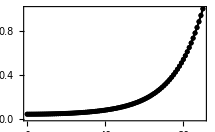
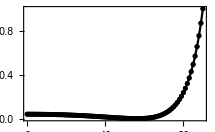

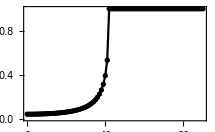
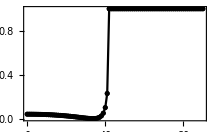

```mathematica
ang = Range[0,90,1.]*Pi/180.;
lda = 500.
ind = Transpose[{1.,1.,1.5}&@ lda];

CSM3MediaReflectionExt[ang, ind, lda, 100., .2] ;
ListLinePlot[Transpose@#,DataRange->{0,90}, PlotRange->All]& /@ Chop[#*Conjugate[#]]&[%]
CSM3MediaReflectionInt[ang, ind, lda, 50., .1];
ListLinePlot[Transpose@#,DataRange->{0,90}, PlotRange->All]& /@ Chop[#*Conjugate[#]]&[%]
```

#### CSM3MediaTransmissionExt - CSM3MediaTransmissionInt [ang, {nM,nP, nS},lda, rad,cfrac] = {rs, rp}

```mathematica
CSM3MediaTransmissionExt[ang_,{nM_,nP_,nS_},lda_,rad_,cfrac_]:=Module[{thetai = toMap[ang], wlength = toMap[lda], rtCoh, rt13, beta, func,tt},
If[Length[rad]!=0,Return[Message[CoherentScatteringModel::radius,rad]]];
If[Length[cfrac]!=0,Return[Message[CoherentScatteringModel::cfrac,cfrac]]];
If[!Apply[Equal, Length /@ {lda, nM,nP}], Return[Message[CoherentScatteringModel::length,nP,nM,lda]]];

rtCoh= CSMAmplitudeReflectionTransmission[thetai,toMap/@{nM,nP}, wlength, rad, cfrac]; (*[[pol, rt, ang, lda]]*)
rt13= Through[{FresnelReflectionS,FresnelTransmissionS, FresnelReflectionP,FresnelTransmissionP}[thetai, toMap/@{nM,nS}]]; (*[[4, ang, lda*)
rt13= Partition[rt13,2];(*[[pol, rt, ang, lda*)
 beta = (2.*Pi/wlength)*(2*rad)*toMap[nM] * # &/@ Cos[thetai];  (*[[ang, lda]]*)

func = ( #1[[2]]* #2[[2]] *Exp[I*beta])/(1.- #1[[1]]* #2[[1]] *Exp[2*I*beta])   & ;
tt = MapThread[func ][ {rtCoh, rt13}] ;(*[[pol (2), ang, lda]]*)

Which[Length[nM]==Length[ang]==0, tt[[;;,1,1]],
	Length[nM]==0 , tt[[;;,;;,1]],
	 Length[ang]== 0, tt[[;;,1,;;]],
	True, tt]
]
```

```mathematica
CSM3MediaTransmissionInt[ang_,{nM_,nP_,nS_},lda_,rad_,cfrac_]:=Module[{thetai = toMap[ang],thetat, wlength = toMap[lda], rtCoh, r13t31, beta, func,tt},
If[Length[rad]!=0,Return[Message[CoherentScatteringModel::radius,rad]]];
If[Length[cfrac]!=0,Return[Message[CoherentScatteringModel::cfrac,cfrac]]];
If[!Apply[Equal, Length /@ {lda, nM,nP}], Return[Message[CoherentScatteringModel::length,nP,nM,lda]]];

thetat = ArcSin[ #* toMap[ nS/nM] ] &/@ Sin[thetai] ; (* [[ang, lda]] *)

rtCoh = Array[   CSMAmplitudeReflectionTransmission[ thetat[[#1,#2]],Map[toMap,{nM,nP}][[;;, #2]], wlength[[#2]], rad, cfrac]& , Dimensions[thetat]] ; (*[[ang, lda, pol, rt]]*)
rtCoh = Transpose[rtCoh, {3,4,1,2}]; (*[[pol, rt, ang, lda]]*)
r13t31 = Through[{FresnelReflectionS, FresnelReflectionP}[thetai, toMap/@{nM,nS}]]; (*[[pol, ang, lda]]*)
r13t31 = Partition[#,2]&@Join[r13t31,  Through[{FresnelTransmissionS, FresnelTransmissionP}[thetai, toMap/@{nS,nM}]]]; (*[[rt, pol, ang, lda]]*)
r13t31 = Transpose[r13t31]; (*[[pol, rt, ang, lda]]*)
beta = (2.*Pi/wlength)*(2.*rad)*toMap[nM]*# & /@ Cos[thetat]; (*[[ang, lda]]*)

func = ( #1[[2]]* #2[[2]] *Exp[I*beta])/(1.- #1[[1]]* #2[[1]] *Exp[2*I*beta])   & ;
tt = MapThread[func ][ {rtCoh, r13t31}] ;(*[[pol (2), ang, lda]]*)

Which[Length[nM]==Length[ang]==0, tt[[;;,1,1]],
	Length[nM]==0 , tt[[;;,;;,1]],
	 Length[ang]== 0, tt[[;;,1,;;]],
	True, tt]
]
```

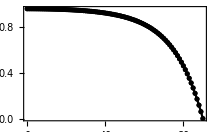
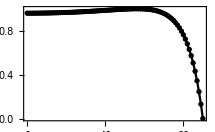

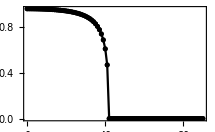
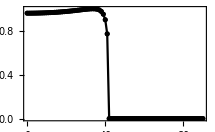

```mathematica
ang = Range[0,90,1.]*Pi/180.;
lda = 500.;
ind = Transpose[{1.,1.,1.5}&@ lda];

CSM3MediaTransmissionExt[ang, ind, lda, 100., .2] ;
{#,#}&@Sqrt@FresnelImpedance[ang,ind[[{1,3}]]];
ListLinePlot[Transpose@#,DataRange->{0,90}, PlotRange->All]& /@ Chop[#*Conjugate[#]]&[%*%%]
CSM3MediaTransmissionInt[ang, ind, lda, 50., .1];
{#,#}&@Sqrt@FresnelImpedance[ang,ind[[{3,1}]]];
ListLinePlot[Transpose@#,DataRange->{0,90}, PlotRange->All]& /@ Chop[#*Conjugate[#]]&[%*%%]
```

#### CSM3MediaElipsometryExt - CSM3MediaElipsometryInt

```mathematica
CSM3MediaElipsometryExt[ang_,{nM_,nP_,nS_},lda_,rad_,cfrac_]:= {ArcTan[Abs[#]],Arg[#]}&@ (Divide@@ CSM3MediaReflectionExt[ang,{nM,nP,nS},lda,rad,cfrac](*[[pol (2), ang, lda]]*)) 
CSM3MediaElipsometryInt[ang_,{nM_,nP_,nS_},lda_,rad_,cfrac_]:= {ArcTan[Abs[#]],Arg[#]}&@ (Divide@@ CSM3MediaReflectionInt[ang,{nM,nP,nS},lda,rad,cfrac](*[[pol (2), ang, lda]]*))
```

### Dipolar Model

```mathematica
DipolarModel::cfrac = "The coverage fraction `1` must be a scalar.";
DipolarModel::length = "The Length of `1`, `2` and `3` must be the same.";
```

#### Disordered cases (Internal end External case) DMDielecticFunctionExt[{nM_,nP_,nS_},cfrac_] = {epsPara, epsPerp}

```mathematica
DMDielecticFunctionExt[{nM_,nP_,nS_},cfrac_]:=Module[{alpha, A, g=1., gI = Sqrt[2.]/4.,eps, epsDM = {0,0}},
If[!Apply[Equal,Length/@ {nM,nP,nS}], Return[Message[DipolarModel::length, nM,nP,nS]]];
If[Length[cfrac]!=0, Return[Message[DipolarModel::cfrac, cfrac]]];

eps = Map[toMap[#]^2&,{nM,nP,nS}]; (*[[3, nM]] *)
A =  Apply[Divide  , {Plus[#1,-#2],Plus[#1,#2]}]& @@eps[[{3,1}]];
alpha =  Apply[Divide  , {Plus[#1,-#2],Plus[#1,2*#2]}]& @@eps[[{2,1}]];

epsDM[[1]] = eps[[1]] * (1. + (2.*cfrac*alpha)/ (1.-alpha*( 0.125 * A +.5 *(g-A*gI)*cfrac  )));
epsDM[[2]] = eps[[1]] / (1. - (2.*cfrac*alpha)/ (1.-alpha*( 0.25 * A -(g-A*gI)*cfrac  )));

If[Length[nM]==0, epsDM[[;;,1]], Transpose[epsDM]]]
```

#### Disordered cases (Internal end External case) DMDielecticFunctionInt[{nM_, nP_, nS_}, cfrac_] = {epsPara, epsPerp}

```mathematica
DMDielecticFunctionInt[{nS_,nP_,nM_},cfrac_]:=Module[{alpha, A, g=1., gI = Sqrt[2.]/4.,eps, epsDM = {0,0}},
If[!Apply[Equal,Length/@ {nM,nP,nS}], Return[Message[DipolarModel::length, nM,nP,nS]]];
If[Length[cfrac]!=0, Return[Message[DipolarModel::cfrac, cfrac]]];

eps = Map[toMap[#]^2&,{nS,nP,nM}]; (*[[3, nM]] *)
A =  -Apply[Divide  , {Plus[#1,-#2],Plus[#1,#2]}]& @@eps[[{3,1}]];
alpha =  Apply[Divide  , {Plus[#1,-#2],Plus[#1,2*#2]}]& @@eps[[{2,3}]];

epsDM[[1]] = eps[[3]] * (1. + (2.*cfrac*alpha)/ (1.-alpha*( 0.125 * A +0.5 *(g-A*gI)*cfrac  )));
epsDM[[2]] = 1. / ((1/eps[[3]]) - (2.*cfrac*alpha/eps[[1]])/ (1.-alpha*( 0.25 * A -(g-A*gI)*cfrac  )));

If[Length[nM]==0, epsDM[[;;,1]], Transpose[epsDM]]]
```

{1.53828+0.350272 ⅈ,1.53934+0.350518 ⅈ,1.54028+0.35128 ⅈ,1.54072+0.35188 ⅈ,1.54049+0.352059 ⅈ,1.53986+0.352499 ⅈ,1.5392+0.354024 ⅈ,1.53883+0.357431 ⅈ,1.53865+0.362649 ⅈ,1.53822+0.368932 ⅈ,1.53705+0.375443 ⅈ,1.53463+0.381348 ⅈ,1.53119+0.386916 ⅈ,1.52739+0.393117 ⅈ,1.5239+0.401105 ⅈ,1.5215+0.412274 ⅈ,1.52112+0.427804 ⅈ,1.52398+0.448359 ⅈ,1.53206+0.474595 ⅈ,1.5485+0.50688 ⅈ,1.57796+0.544376 ⅈ,1.62498+0.582717 ⅈ,1.69146+0.613135 ⅈ,1.77322+0.624236 ⅈ,1.85754+0.607791 ⅈ,1.92763+0.565827 ⅈ,1.97472+0.509682 ⅈ,2.00046+0.450554 ⅈ,2.01041+0.39504 ⅈ,2.01035+0.345614 ⅈ,2.00473+0.302323 ⅈ,1.99639+0.264223 ⅈ,1.98626+0.230598 ⅈ,1.97469+0.201032 ⅈ,1.96203+0.17519 ⅈ,1.94858+0.152777 ⅈ,1.93463+0.133516 ⅈ,1.92042+0.117129 ⅈ,1.90628+0.103283 ⅈ,1.89258+0.0915804 ⅈ,1.87953+0.0816533 ⅈ}

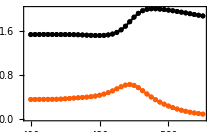

```mathematica
wlength = Range[400,600,5];
indices = Transpose[Map[{1.5, nAuSize[#,18.],1.}&,wlength]];
DMDielecticFunctionInt[ indices, .25][[;;,1]]
Transpose@ReIm@DMDielecticFunctionInt[ indices, .25][[;;,1]] //ListLinePlot[#,DataRange-> {400,600}]&
```

## Ellipsometric Parameters

```mathematica
ZeroToPi = If[#<0,2.*Pi+#,#]&;
derivable[list_]:=Module[{pos},
pos = Flatten[Position[list,#]&/@MinMax[list]];
If[Abs[pos[[1]]-pos[[2]]]==1,Map[ZeroToPi,list],list]
]

ZeroToMinusPi = If[#>0,-2*Pi-#,#]&;

derivable2[list_]:=Module[{pos},
pos = Flatten[Position[list,#]&/@MinMax[list]];
If[Abs[pos[[1]]-pos[[2]]]==1,Join[list[[1;;pos[[1]]]],-2*Pi+list[[pos[[2]];;-1]]],list]
]

derivable3[list_]:=Module[{pos},
pos = Reverse@Flatten[Position[list,#]&/@MinMax[list]];
If[Abs[pos[[1]]-pos[[2]]]==1,Join[list[[1;;pos[[1]]]],+2*Pi+list[[pos[[2]];;-1]]],list]
]
```

## Single Particle

```mathematica
CreateDirectory[dir = "1.- Single Particle"]
```

CreateDirectory::eexist: /home/jonathan/Dropbox/WorkWithAlejandro/4.- MScThesis/1.- Single Particle already exists.

$Failed

### Qsca & Qext - Size Correction vs. No Correction

```mathematica
dir = "1.- Single Particle"
radius = 50.;
plots = ConstantArray[0,{2,2}];
ampFactor = 1.;
ar = 1/2.75;
```

1.- Single Particle

#### No Size Correction

```mathematica
nNP = nAuFunc;
wlength = Range[400,700,2.5];
max = scaQ = extQ = {0,0};
scaFunc[lda_]:= Map[ampFactor*MieScatteringQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
extFunc[lda_]:=  Map[MieExtintionQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];

nMat = 1. &;
extQ[[1]] = extFunc[wlength];
scaQ[[1]] = scaFunc[wlength];
max[[1]]=FindExtrema[#, wlength[[{1,-1}]], 10., "Maxima"][[1,1]] &/@ {extFunc,scaFunc};


nMat = nH2OFunc;
extQ[[2]] = extFunc[wlength];
scaQ[[2]] = scaFunc[wlength];
max[[2]] = FindExtrema[#, wlength[[{1,-1}]], 10., "Maxima"][[1,1]]  &/@ {extFunc,scaFunc};

max = Transpose[max];
```

```mathematica
plots[[1]] = MapThread[Show[{
ListLinePlot[#, AspectRatio->ar,Mesh->None, DataRange->wlength[[{1,-1}]]],
ListPlot[Callout[#,Style["~"<>ToString[IntegerPart@#[[1]]]<>" nm" , texStyle],Right]&/@#2]
},PlotRange-> All]&,{{extQ,scaQ}, max}]

Column[%,Spacings->0]
```

{-Graphics-,-Graphics-}

-Graphics-

#### Size Correction

```mathematica
nNP = nAuSize[#,radius]&;
wlength = Range[400,700,2.5];
max = scaQ = extQ = {0,0};
scaFunc[lda_]:= Map[ampFactor*MieScatteringQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
extFunc[lda_]:=  Map[MieExtintionQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];

nMat = 1. &;
extQ[[1]] = extFunc[wlength];
scaQ[[1]] = scaFunc[wlength];
max[[1]]=FindExtrema[#, wlength[[{1,-1}]], 10., "Maxima"][[1,1]] &/@ {extFunc,scaFunc};


nMat = nH2OFunc;
extQ[[2]] = extFunc[wlength];
scaQ[[2]] = scaFunc[wlength];
max[[2]] = FindExtrema[#, wlength[[{1,-1}]], 10., "Maxima"][[1,1]]  &/@ {extFunc,scaFunc};

max = Transpose[max];
```

```mathematica
plots[[2]] = MapThread[Show[{
ListLinePlot[#, PlotStyle -> {Directive[ColorData[3,1],Dashed],Directive[ColorData[3,2],Dashed]},
AspectRatio->ar,Mesh->None, DataRange->wlength[[{1,-1}]]],
ListPlot[Callout[#,Style["~"<>ToString[IntegerPart@#[[1]]]<>" nm" , texStyle],Right]&/@#2]
},PlotRange-> All]&,{{extQ,scaQ}, max}]

Column[%,Spacings->0]
```

{-Graphics-,-Graphics-}

-Graphics-

#### Results

```mathematica
flabels = {{None,MaTeX["Q_\\text{ext}",FontSize->fs, ContentPadding->False]},MaTeX[{ "\\lambda\\text{ [nm]}","Q_\\text{sca} \\times"<>ToString[ampFactor]},FontSize->fs, ContentPadding->False]}
LineLegend[{Directive[Gray],Directive[Gray,Dashed]}, Style[#,texStyle]&/@{"No Size Correction","Size Correction"},Spacings-> 0.0,LegendMarkerSize->10];
LineLegend[{Directive[Black],Directive[Orange]}, Style[#,texStyle]&/@{"@Air","@H_2O"},Spacings-> .0,LegendMarkerSize->10,LegendLabel->Style[ToString[radius]<>" nm AuNP",texStyle ]];
legend = Reverse@{Column[{%,%%},Spacings->-.5],Null}

MapThread[Show,plots];
Column@MapThread[Show[#,FrameLabel-> #2, Epilog-> Inset[#3,{550,2.5}]]&,{%, flabels,legend}]
Export[FileNameJoin[{dir,"QextQsca.svg"}],%]
```

{{None,-Graphics-},{-Graphics-,-Graphics-}}

{Null,
}

-Graphics-

2.- Single Particle/QextQsca.svg

### RedShift

```mathematica
dir = "2.- Single Particle"
plots = ConstantArray[0,{2,2,2}];
radList = Range[5,50,2.];
nMatList = Range[1.,1.8,.04];
(*color-> ext/sca  marcador -> aire/agua -- 12/50,  abierto/cerrado -> correccion*)
markers = {{"●","●",  "○", "○"},{"●","●",  "○", "○"}};
```

2.- Single Particle

#### Radius

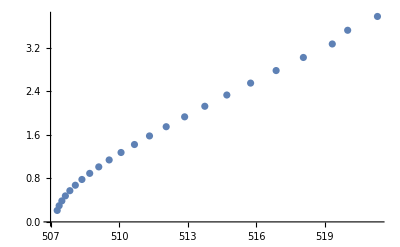
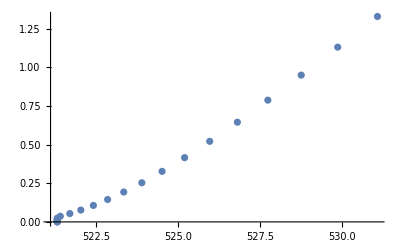

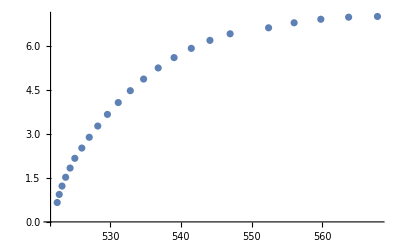
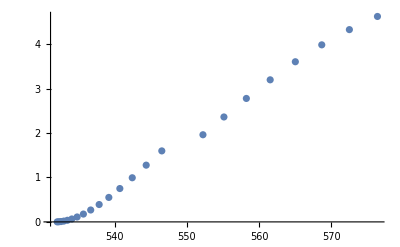

```mathematica
ClearAll[radius]
nNP = nAuFunc;
wlength = {490.,700.};
air = h20= plots[[1]];

scaFunc[lda_]:= MieScatteringQ[{nMat[lda],nNP[lda]},lda,radius]
extFunc[lda_]:=  MieExtintionQ[{nMat[lda],nNP[lda]},lda,radius]
nMat = 1. &;
air[[1]] =Table[radius = rr;
		 FindExtrema[#,wlength, 5., "Maxima"][[1]],
		{rr,radList}]&/@ {extFunc,scaFunc};
nMat = nH2OFunc;
h20[[1]] =Table[radius = rr;
		 FindExtrema[#,wlength, 2.5, "Maxima"][[1]],
		{rr,radList}]&/@ {extFunc,scaFunc};
ListPlot /@ air[[1]]
ListPlot/@ h20[[1]]
```

```mathematica
plots[[1,1]] = MapThread[ListPlot[Transpose[{radList,#}]&/@ #[[;;,;;,1]], Mesh->None,PlotMarkers->#2,graphsOpts, PlotRange->{{3,52},{Automatic,Automatic}}]&,{{air[[1]],h20[[1]]},markers}];
```

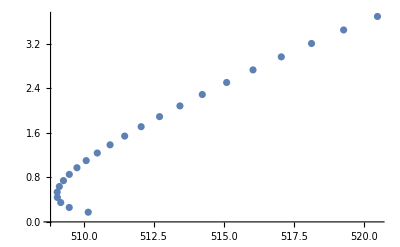
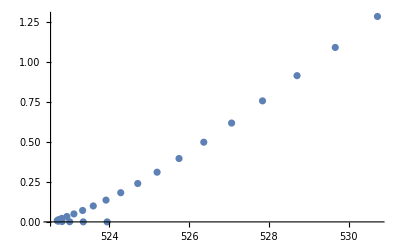

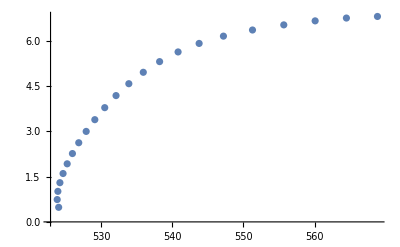
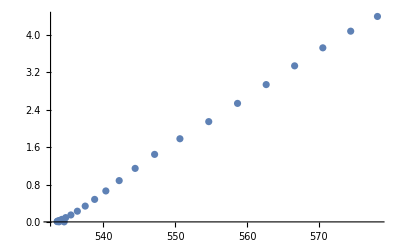

```mathematica
nNP:=nAuSize[#,radius]&

nMat = 1. &;
air[[2]] =Table[radius = rr;
		 FindExtrema[#,wlength, 5., "Maxima"][[1]],
		{rr,radList}]&/@ {extFunc,scaFunc};
nMat = nH2OFunc;
h20[[2]] =Table[radius = rr;
		 FindExtrema[#,wlength, 2.5, "Maxima"][[1]],
		{rr,radList}]&/@ {extFunc,scaFunc};
ListPlot /@ air[[2]]
ListPlot/@ h20[[2]]
```

```mathematica
plots[[1,2]] = MapThread[ListPlot[Transpose[{radList,#}]&/@ #[[;;,;;,1]], Mesh->None,PlotMarkers->Reverse@#2,graphsOpts, PlotRange->{{3,52},{Automatic,Automatic}}]&,{{air[[2]],h20[[2]]},markers}];
```

#### Matrix

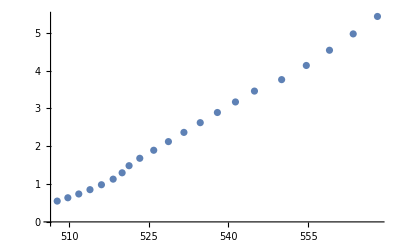
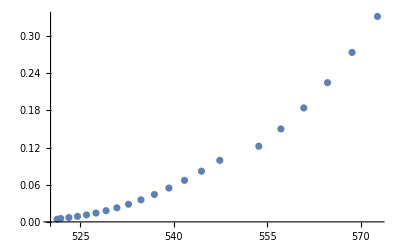

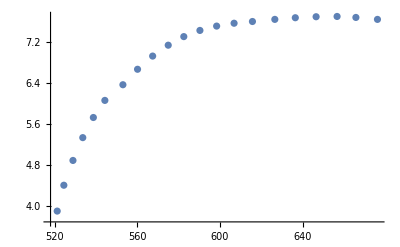
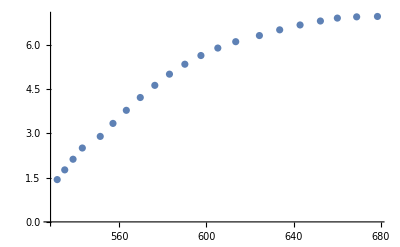

```mathematica
ClearAll[radius]
nNP = nAuFunc;
wlength = {490.,750.};
r12 = r50= plots[[2]];

scaFunc[lda_]:= MieScatteringQ[{nMat[lda],nNP[lda]},lda,radius]
extFunc[lda_]:=  MieExtintionQ[{nMat[lda],nNP[lda]},lda,radius]

radius = 12.5;
r12[[1]] =Table[nMat = nm &;
		 FindExtrema[#,wlength, 5., "Maxima"][[1]],
		{nm,nMatList}]&/@ {extFunc,scaFunc};
radius = 50.;
r50[[1]] =Table[nMat = nm &;
		 FindExtrema[#,wlength, 5., "Maxima"][[-1]],
		{nm,nMatList}]&/@ {extFunc,scaFunc};
ListPlot /@ r12[[1]]
ListPlot/@ r50[[1]]
```

```mathematica
plots[[2,1]] = MapThread[ListPlot[Transpose[{nMatList,#}]&/@ #[[;;,;;,1]], Mesh->None,PlotMarkers->#2,graphsOpts]&,{{r12[[1]],r50[[1]]},markers}];
```

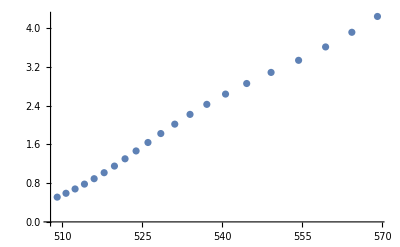
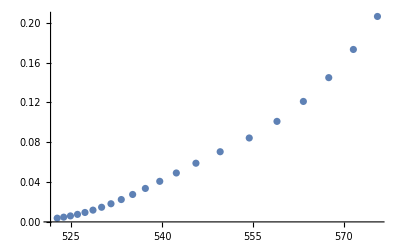

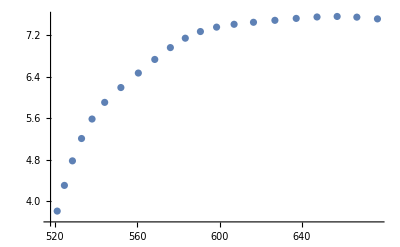
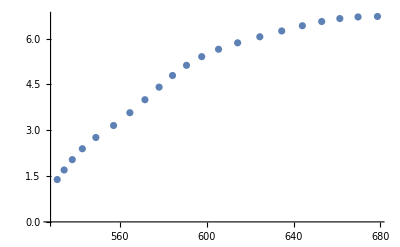

```mathematica
nNP:=nAuSize[#,radius]&

radius = 12.5;
r12[[2]] =Table[nMat = nm &;
		 FindExtrema[#,wlength, 5., "Maxima"][[1]],
		{nm,nMatList}]&/@ {extFunc,scaFunc};
radius = 50.;
r50[[2]] =Table[nMat = nm &;
		 FindExtrema[#,wlength, 5., "Maxima"][[-1]],
		{nm,nMatList}]&/@ {extFunc,scaFunc};
ListPlot /@ r12[[2]]
ListPlot /@ r50[[2]]
```

```mathematica
plots[[2,2]] = MapThread[ListPlot[Transpose[{nMatList,#}]&/@ #[[;;,;;,1]], Mesh->None,PlotMarkers->Reverse@#2,graphsOpts]&,{{r12[[2]],r50[[2]]},markers}];
```

#### Results

```mathematica
flabels ={{#,#}&@ MaTeX[{"\\text{Radius }a\\text{ [nm]}","\\lambda_\\text{res}\\text{ [nm]}"},ContentPadding->False,FontSize->fs],
{#,#}&@ MaTeX[{"\\text{Matrix }n_m\\text{ [RIU]}","\\lambda_\\text{res}\\text{ [nm]}"},ContentPadding->False,FontSize->fs]};

PointLegend[{Directive[Gray],Directive[Gray]}, Style[#,texStyle]&/@{"No Size Correction","Size Correction"},Spacings-> 0.5,LegendMarkers->markers[[1,{1,-1}]],LegendMarkerSize->15, LegendLayout->"Row"];
LineLegend[{Directive[Black],Directive[Orange]}, Style[ #,texStyle]&/@{"Extintion","Scattering"},Spacings-> .5, LegendMarkerSize->15,LegendLayout->"Row"]
legend = Framed[Row[{%%,%}],RoundingRadius->10];
Export[FileNameJoin[{dir,"legend.svg"}],%]
plotLabels = Map[Style[#,texStyle]&,{{"AuNP@Air","AuNP@H_2O"},{"12.5 nm AuNP","50 nm AuNP"}},{2}];
```

2.- Single Particle/legend.svg

```mathematica
flabels = flabels ={{#,#}&@{"Radius: $a$ [nm]","$\lambda_\\text{res}$ [nm]"},
{#,#}&@{"Matrix: $n_\\text{m}$ [RIU]", "$\lambda_\\text{res}$ [nm]"}}
plotLabels = Map[Style[#,texStyle]&,{{"AuNP@Air","AuNP@H_2O"},{"12.5 nm AuNP","50 nm AuNP"}},{2}];
```

{{{Radius: $a$ [nm],$\lambda_\text{res}$ [nm]},{Radius: $a$ [nm],$\lambda_\text{res}$ [nm]}},{{Matrix: $n_\text{m}$ [RIU],$\lambda_\text{res}$ [nm]},{Matrix: $n_\text{m}$ [RIU],$\lambda_\text{res}$ [nm]}}}

```mathematica
MapThread[Show[{#1,#2}, FrameLabel-> #3]&, Append[Transpose[plots],flabels],2];
Row@Flatten@Map[Show[#1, AspectRatio-> 2, ImageSize-> 215/1.8]&, %, {2}]
Export[FileNameJoin[{dir,"redShift2.pdf"}],%]
```

-Graphics--Graphics--Graphics--Graphics-

2.- Single Particle/redShift2.pdf

```mathematica
MapThread[Show[{#1,#2}]&, Transpose[plots],2];
Row@Flatten@Map[Show[#1, AspectRatio-> 2, ImageSize-> 215/1.8]&, %, {2}]
Export[FileNameJoin[{dir,"redShift1SVG.svg"}],%]
```

-Graphics--Graphics--Graphics--Graphics-

2.- Single Particle/redShift1SVG.svg

## Electric Field

```mathematica
eV = Range[2,8,.001];
wp = 10.;gamma = .0001;(*eV*)
radius = 20;

nMat = 1.&
nNP[w_]:= Sqrt[1-wp^2/(w*(w+I*gamma))]
extFunc[lda_]:=  Map[MieExtintionQ[{nMat[#],nNP[hc/#]},#,radius]&,toMap[lda]];


extrema = FindExtrema[extFunc, Sort[hc/{2,8}],1,"Maxima" ][[1]]/.{a_,b_}->{hc/a,b}
Show[{ListLinePlot[Transpose[{#,extFunc[hc/#]}]&[eV],PlotRange->All],
ListPlot@MapIndexed[Callout[#1,Style["l = "<>ToString[First[#2]],texStyle]]&,Reverse@extrema]}
]
```

1.&

{{6.49289,1.28922},{6.42564,1.39292},{6.17,3.06349},{6.12853,27.8111},{5.17201,21.8151}}

-Graphics-

```mathematica
mesh = Array[{#1+.1,0.,#2+.1}&,{50,50},{-#,#}&[1.5*radius]];
AbsoluteTiming[data = MieElectricField[mesh,{nMat[#],nNP[hc/#]},#,radius]&[hc/extrema[[-1,1]]];]
```

{46.7773,Null}

```mathematica
mesh = Array[{#1,0,#2}&,{100,100},{-#,#}&[1.5*radius]];
AbsoluteTiming[data = MieElectricField[mesh,{nMat[#],nNP[hc/#]},#,radius]&[hc/extrema[[2,1]]];]
```

{213.223,Null}

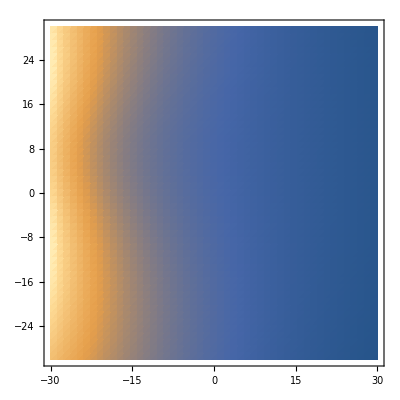

```mathematica
ListDensityPlot[Map[Norm,data,{2}],DataRange->{{-#,#},{-#,#}}&[1.5*radius],PlotRange->All]
```

## Multipoles on a Au Sphere

```mathematica
plots = ConstantArray[0,{2,2}];
wlength = {490.,700.};
lda = Range[490,700,10];
```

```mathematica
ClearAll[radius]
nNP = nAuFunc;
radius = 80.;

scaFunc[lda_]:= Map[MieScatteringQ[{nMat[#],nNP[#]},#,radius]&,lda]
extFunc[lda_]:=   Map[MieExtintionQ[{nMat[#],nNP[#]},#,radius]&,lda]
nMat = 2 &;
```

### Qsca & Qext - Size Correction vs. No Correction

```mathematica
CreateDirectory[dir = "2.- Multipolar Contribution"]
plots = ConstantArray[0,{2,2}];
ampFactor = 1.;
ar = 1/2.75;
```

CreateDirectory::eexist: /home/jonathan/Dropbox/WorkWithAlejandro/4.- MScThesis/2.- Multipolar Contribution already exists.

$Failed

#### No Size Correction Wacombe

```mathematica
nNP = nAuFunc;
wlength = Range[400,900,2.5];
max = scaQ = extQ = ConstantArray[0,{3,2}];

scaFunc[lda_]:= Map[ampFactor*MieScatteringQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
extFunc[lda_]:=  Map[MieExtintionQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
scaFuncN[lda_,nn_]:= Map[ampFactor*MieScatteringQ[{nMat[#],nNP[#]},#,radius,nn]&,toMap[lda]];
extFuncN[lda_,nn_]:=  Map[MieExtintionQ[{nMat[#],nNP[#]},#,radius,nn]&,toMap[lda]];

Table[
If[j == 1, nMat = 1.33 &, nMat = 1.5& ];

extQ[[1,j]] = extFunc[wlength];
scaQ[[1,j]] = scaFunc[wlength];
max[[1,j]]=FindExtrema[#, wlength[[{1,-1}]], 10., "Maxima"][[1,1]] &/@ {extFunc,scaFunc};

Table[
extQ[[1+i,j]] = extFuncN[wlength,{i}];
scaQ[[1+i,j]] = scaFuncN[wlength,{i}];
max[[1+i,j]]=FindExtrema[#, wlength[[{1,-1}]], 10., "Maxima"][[1,1]] &/@ {extFuncN[#,i]&,scaFuncN[#,i]&};
,{i,2}]
,{j,2}]
```

{{Null,Null},{Null,Null}}

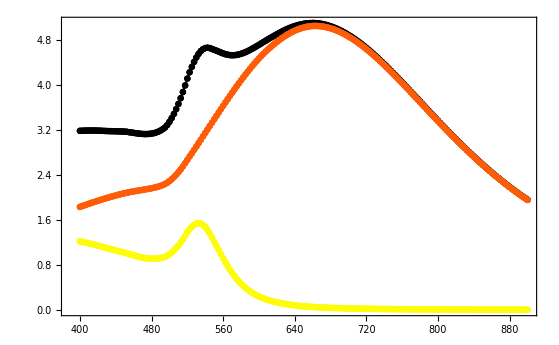

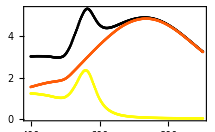

```mathematica
ListLinePlot[extQ[[;;,1]],DataRange->{400,900}]
ListLinePlot[extQ[[;;,2]],DataRange->{400,900}]
```

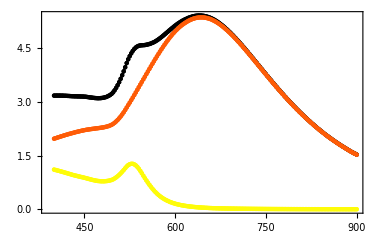

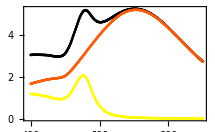

```mathematica
ListLinePlot[extQ[[;;,1]],DataRange->{400,900}]
ListLinePlot[extQ[[;;,2]],DataRange->{400,900}]
```

```mathematica
Dimensions[max]
```

{3,2,2,2}

```mathematica
plots[[1]] = MapThread[Show[{
ListLinePlot[#1, AspectRatio->ar,Mesh->None, DataRange->wlength[[{1,-1}]]],
ListPlot[Callout[#,Style["~"<>ToString[IntegerPart@#[[1]]]<>" nm" , texStyle],Right]&/@#3]
},PlotRange-> All]&,{extQ,scaQ, max}]

Column[%,Spacings->0]
```

{-Graphics-,-Graphics-,-Graphics-}

-Graphics-

#### No Size Correction Lmax

```mathematica
nNP = nAuFunc;
wlength = Range[400,900,2.5];
max = scaQ = extQ = ConstantArray[0,{3,2}];

Ceiling[#+4.*#^(1./3)+2.]&/@(2Pi*radius*1.8/wlength);
Max[%]
lMax = 15;
```

8

```mathematica
scaFunc[lda_]:= Map[ampFactor*MieScatteringQ[{nMat[#],nNP[#]},#,radius,lMax]&,toMap[lda]];
extFunc[lda_]:=  Map[MieExtintionQ[{nMat[#],nNP[#]},#,radius,lMax]&,toMap[lda]];
scaFuncN[lda_,nn_]:= Map[ampFactor*MieScatteringQ[{nMat[#],nNP[#]},#,radius,nn]&,toMap[lda]];
extFuncN[lda_,nn_]:=  Map[MieExtintionQ[{nMat[#],nNP[#]},#,radius,nn]&,toMap[lda]];

Table[
If[j == 1, nMat = 1. &, nMat = 2.& ];

extQ[[1,j]] = extFunc[wlength];
scaQ[[1,j]] = scaFunc[wlength];
max[[1,j]]=FindExtrema[#, wlength[[{1,-1}]], 10., "Maxima"][[1,1]] &/@ {extFunc,scaFunc};

Table[
extQ[[1+i,j]] = extFuncN[wlength,{i}];
scaQ[[1+i,j]] = scaFuncN[wlength,{i}];
max[[1+i,j]]=FindExtrema[#, wlength[[{1,-1}]], 10., "Maxima"][[1,1]] &/@ {extFuncN[#,i]&,scaFuncN[#,i]&};
,{i,2}]
,{j,2}]
```

{{Null,Null},{Null,Null}}

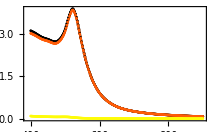

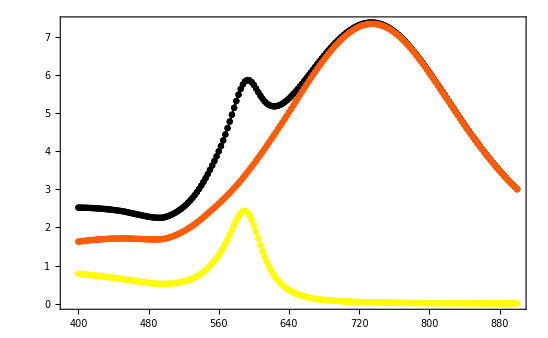

```mathematica
ListLinePlot[extQ[[;;,1]],DataRange->{400,900}]
ListLinePlot[extQ[[;;,2]],DataRange->{400,900}]
```

-Graphics-

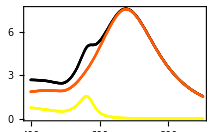

```mathematica
ListLinePlot[extQ[[;;,1]],DataRange->{400,900}]
ListLinePlot[extQ[[;;,2]],DataRange->{400,900}]
```

```mathematica
Dimensions[max]
```

{3,2,2,2}

```mathematica
plots[[1]] = MapThread[Show[{
ListLinePlot[#1, AspectRatio->ar,Mesh->None, DataRange->wlength[[{1,-1}]]],
ListPlot[Callout[#,Style["~"<>ToString[IntegerPart@#[[1]]]<>" nm" , texStyle],Right]&/@#3]
},PlotRange-> All]&,{extQ,scaQ, max}]

Column[%,Spacings->0]
```

{-Graphics-,-Graphics-,-Graphics-}

-Graphics-

#### Size Correction

```mathematica
nNP = nAuSize[#,radius]&;
wlength = Range[400,700,2.5];
max = scaQ = extQ = {0,0};
scaFunc[lda_]:= Map[ampFactor*MieScatteringQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
extFunc[lda_]:=  Map[MieExtintionQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];

nMat = 1. &;
extQ[[1]] = extFunc[wlength];
scaQ[[1]] = scaFunc[wlength];
max[[1]]=FindExtrema[#, wlength[[{1,-1}]], 10., "Maxima"][[1,1]] &/@ {extFunc,scaFunc};


nMat = nH2OFunc;
extQ[[2]] = extFunc[wlength];
scaQ[[2]] = scaFunc[wlength];
max[[2]] = FindExtrema[#, wlength[[{1,-1}]], 10., "Maxima"][[1,1]]  &/@ {extFunc,scaFunc};

max = Transpose[max];
```

```mathematica
plots[[2]] = MapThread[Show[{
ListLinePlot[#, PlotStyle -> {Directive[ColorData[3,1],Dashed],Directive[ColorData[3,2],Dashed]},
AspectRatio->ar,Mesh->None, DataRange->wlength[[{1,-1}]]],
ListPlot[Callout[#,Style["~"<>ToString[IntegerPart@#[[1]]]<>" nm" , texStyle],Right]&/@#2]
},PlotRange-> All]&,{{extQ,scaQ}, max}]

Column[%,Spacings->0]
```

{-Graphics-,-Graphics-}

-Graphics-

#### Results

```mathematica
flabels = {{None,MaTeX["Q_\\text{ext}",FontSize->fs, ContentPadding->False]},MaTeX[{ "\\lambda\\text{ [nm]}","Q_\\text{sca} \\times"<>ToString[ampFactor]},FontSize->fs, ContentPadding->False]}
LineLegend[{Directive[Gray],Directive[Gray,Dashed]}, Style[#,texStyle]&/@{"No Size Correction","Size Correction"},Spacings-> 0.0,LegendMarkerSize->10];
LineLegend[{Directive[Black],Directive[Orange]}, Style[#,texStyle]&/@{"@Air","@H_2O"},Spacings-> .0,LegendMarkerSize->10,LegendLabel->Style[ToString[radius]<>" nm AuNP",texStyle ]];
legend = Reverse@{Column[{%,%%},Spacings->-.5],Null}

MapThread[Show,plots];
Column@MapThread[Show[#,FrameLabel-> #2, Epilog-> Inset[#3,{550,2.5}]]&,{%, flabels,legend}]
Export[FileNameJoin[{dir,"QextQsca.svg"}],%]
```

{{None,-Graphics-},{-Graphics-,-Graphics-}}

{Null,
}

-Graphics-

2.- Single Particle/QextQsca.svg